```mathematica
Get["NeutronBeam/NBeam_IntTables.m"]
Get["NeutronBeam/XYBinIntBoundaries.m"]
```

Set::wrsym: Symbol pmax is Protected.

```mathematica
Get["NeutronBeam/NBeamIntegrand.m"]
```

Set::wrsym: Symbol pmax is Protected.

```mathematica
IntegrationRules={"GaussBerntsenEspelidRule","GaussKronrodRule","LobattoKronrodRule","ClenshawCurtisRule","CartesianRule","MultidimensionalRule"};
IntegrationStrategies={"GlobalAdaptive","LocalAdaptive"};
IntOptionList=Flatten[Table[
{strategy,Method->rule},
{strategy,IntegrationStrategies},{rule,IntegrationRules}],1]
```

{{GlobalAdaptive,Method→GaussBerntsenEspelidRule},{GlobalAdaptive,Method→GaussKronrodRule},{GlobalAdaptive,Method→LobattoKronrodRule},{GlobalAdaptive,Method→ClenshawCurtisRule},{GlobalAdaptive,Method→CartesianRule},{GlobalAdaptive,Method→MultidimensionalRule},{LocalAdaptive,Method→GaussBerntsenEspelidRule},{LocalAdaptive,Method→GaussKronrodRule},{LocalAdaptive,Method→LobattoKronrodRule},{LocalAdaptive,Method→ClenshawCurtisRule},{LocalAdaptive,Method→CartesianRule},{LocalAdaptive,Method→MultidimensionalRule}}

```mathematica
BRxBList={0.15,0.2,0.3,0.4,0.6,0.8,1.,1.2};
```

```mathematica
RoughDriftDistance=Round[Table[D1stBPolyGrad[pmax,Pi,Pi/4,BRxB,1,0.,1,1,1]+2rG[pmax,Pi/4,BRxB]+0.01,{BRxB,BRxBList}],0.01]*0.8
```

{0.112,0.08,0.056,0.048,0.032,0.024,0.024,0.024}

```mathematica
XY35BinsBRamp=Table[XYBinIntBoundaries[{-0.005,xmax-0.005,0.,7},{-0.02,0.02,0.,5}],{xmax,RoughDriftDistance}];
```

```mathematica
BinCentersBRamp=BinCenters[#]&/@XY35BinsBRamp;
```

```mathematica
XOffBRamp=-RoughDriftDistance/2
```

{-0.056,-0.04,-0.028,-0.024,-0.016,-0.012,-0.012,-0.012}

```mathematica
XY35BinsBRampXOff=Table[XYBinIntBoundaries[{-0.005,xmax-0.005,-xmax/2,7},{-0.02,0.02,0.,5}],{xmax,RoughDriftDistance}];
```

```mathematica
BinCentersBRampXOff=BinCenters[#]&/@XY35BinsBRampXOff;
```

```mathematica
Manipulate[Plot3D[pminApertY[phiA,yD,Pi/4,0.2,1.,1.,1.,phiDet,0.,0.035],{phiA,-Pi,Pi},{yD,-0.025,0.025},PlotRange->{0,pmax}],{phiDet,-Pi,Pi}]
```

```mathematica
Manipulate[Plot3D[pmaxApertY[phiA,yD,Pi/4,0.2,1.,1.,1.,phiDet,0.,0.035],{phiA,-Pi,Pi},{yD,-0.025,0.025},PlotRange->{0,pmax}],{phiDet,-Pi,Pi}]
```

```mathematica
Solve[yOff+yAA/2==yA[phiA,yD,plocal,th0,BRxB,rRxB,rA,rD,phiDet],plocal,Reals]
```

{{plocal→ConditionalExpression[(-149896229 BRxB rA rD yAA+299792458 BRxB √(1/rA) rA^(3/2) rD √(rD/rRxB) yD-299792458 BRxB rA rD yOff)/(-rD rRxB Sin[phiA] Sin[th0]+√(1/rA) rA^(3/2) √(rD/rRxB) rRxB Sin[phiDet] Sin[th0]),(rD>0&&rRxB>0&&rA>0)||(rD<0&&rRxB<0&&rA>0)]}}

```mathematica
{{-Pi/2,pminApertY[-Pi/2,0.02,Pi/4,0.2,1.,1.,1.,0,0.,0.035]},{Pi/2,pmaxApertY[Pi/2,0.02,Pi/4,0.2,1.,1.,1.,0,0.,0.035]}}
```

{{-π/2,211985.},{π/2,-3.17978×10^6}}

```mathematica
Manipulate[Show[
Plot[{pminApertY[phiA,yD,Pi/4,0.2,1.,1.,1.,phiDet,0.,0.035],pmaxApertY[phiA,yD,Pi/4,0.2,1.,1.,1.,phiDet,0.,0.035]},{phiA,-Pi,Pi},PlotRange->{-pmax,pmax}],
ListPlot[{{{-Pi/2,pminApertY[-Pi/2,yD,Pi/4,0.2,1.,1.,1.,phiDet,0.,0.035]},{Pi/2,pminApertY[Pi/2,yD,Pi/4,0.2,1.,1.,1.,phiDet,0.,0.035]}},{{-Pi/2,pmaxApertY[-Pi/2,yD,Pi/4,0.2,1.,1.,1.,phiDet,0.,0.035]},{Pi/2,pmaxApertY[Pi/2,yD,Pi/4,0.2,1.,1.,1.,phiDet,0.,0.035]}}}]
],{yD,-0.025,0.025},{phiDet,-Pi,Pi}]
```

General::prng: Value of option PlotRange -> {-pmax,pmax} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

## test some further settings to reduce time

### Prec 4,3,3. Acc 3,3,3. MinRec 0,0,0, MaxRec 2,2,1

```mathematica
BinInt[0.,XY24BinsXOff[[2]],{Pi,0.2,2.,1.,1.,1.,1.,1.,1.},
{0.06,0.05,0.9,0.,-0.9,0.1,0.09,0.9,0.,-0.9},{0.01,0.035,-0.03,0.},{IntOptionList[[6]],4,3,0,2},{IntOptionList[[6]],3,3,0,2},{IntOptionList[[6]],3,3}]//AbsoluteTiming
```

{752.711,0.0460414}

### Prec 4,3,3. Acc 6,6,6. MinRec 0,0,0, MaxRec 2,2,1

```mathematica
BinInt[0.,XY24BinsXOff[[2]],{Pi,0.2,2.,1.,1.,1.,1.,1.,1.},
{0.06,0.05,0.9,0.,-0.9,0.1,0.09,0.9,0.,-0.9},{0.01,0.035,-0.03,0.},{IntOptionList[[6]],4,6,0,2},{IntOptionList[[6]],3,6,0,2},{IntOptionList[[6]],3,6}]//AbsoluteTiming
```

{772.577,0.0460414}

### Prec 3,3,3. Acc 3,3,3. MinRec 0,0,0, MaxRec 2,2,1

```mathematica
BinInt[0.,XY24BinsXOff[[2]],{Pi,0.2,2.,1.,1.,1.,1.,1.,1.},
{0.06,0.05,0.9,0.,-0.9,0.1,0.09,0.9,0.,-0.9},{0.01,0.035,-0.03,0.},{IntOptionList[[6]],3,3,0,2},{IntOptionList[[6]],3,3,0,2},{IntOptionList[[6]],3,3}]//AbsoluteTiming
```

{231.082,0.0460419}

### Prec 3, 3, 3. Acc 3, 3, 3. MinRec 1, 0, 0, MaxRec 2, 2, 1

```mathematica
BinInt[0.,XY24BinsXOff[[2]],{Pi,0.2,2.,1.,1.,1.,1.,1.,1.},
{0.06,0.05,0.9,0.,-0.9,0.1,0.09,0.9,0.,-0.9},{0.01,0.035,-0.03,0.},{IntOptionList[[6]],3,3,1,2},{IntOptionList[[6]],3,3,0,2},{IntOptionList[[6]],3,3}]//AbsoluteTiming
```

{638.068,0.0460414}

## another position!

```mathematica
ParaSet={{4,0},{3,0},{3,1}}
```

{{4,0},{3,0},{3,1}}

```mathematica
$ConfiguredKernels
```

{LightweightGridClient`LightweightGrid[{Agent→http://192.168.0.220:3737/WolframRemoteServices,KernelCount→6,LocalLinkMode→Connect,Service→,Timeout→30}],LightweightGridClient`LightweightGrid[{Agent→http://192.168.0.150:3737/WolframRemoteServices,KernelCount→3,LocalLinkMode→Connect,Service→,Timeout→30}],«3 local kernels»}

```mathematica
CloseKernels[]
LaunchKernels[LightweightGridClient`LightweightGrid[{"Agent"->"http://192.168.0.220:3737/WolframRemoteServices","KernelCount"->3,"LocalLinkMode"->"Connect","Service"->"","Timeout"->30}]]
```

{}

{KernelObject[1,192.168.0.220],KernelObject[2,192.168.0.220],KernelObject[3,192.168.0.220]}

```mathematica
ParallelMap[
(BinInt[0.,XY24BinsXOff[[13]],{Pi,0.2,2.,1.,1.,1.,1.,1.,1.},{0.06,0.05,0.9,0.,-0.9,0.1,0.09,0.9,0.,-0.9},{0.01,0.035,-0.03,0.},
{IntOptionList[[6]],#[[1]],3,#[[2]],2},{IntOptionList[[6]],3,3,0,2},{IntOptionList[[6]],3,4}
]//AbsoluteTiming
)&,ParaSet]
```

{{19000.4,0.245438},{8004.41,0.245427},{16205.6,0.245444}}

```mathematica
0.00001/0.24544//ScientificForm
```

4.07432×10^-5

## First “full” spectrum

```mathematica
ParallelMap[
(BinInt[0.,#,{Pi,0.2,2.,1.,1.,1.,1.,1.,1.},
{0.06,0.05,0.9,0.,-0.9,0.1,0.09,0.9,0.,-0.9},{0.01,0.035,-0.03,0.},{IntOptionList[[6]],4,0},{IntOptionList[[6]],3,0},{IntOptionList[[6]],3}]//AbsoluteTiming)&,XY24BinsXOff]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in xD near {xD,yD} = {0.0246103,0.00422062}. NIntegrate obtained 0.10555 and 0.000113714 for the integral and error estimates.

{{10653.2,0.0351433},{668.225,0.0460414},{655.685,0.0446617},{10145.3,0.0323811},{11436.5,0.152704},{748.562,0.208811},{880.271,0.203576},{14089.,0.143057},{16976.1,0.250381},{1344.98,0.360026},{1372.05,0.354869},{16627.8,0.241296},{23383.4,0.245487},{3350.74,0.362328},{3524.01,0.36293},{22603.6,0.245875},{26486.8,0.159429},{4043.6,0.23859},{6848.8,0.243211},{31198.1,0.167743},{23646.8,0.0659313},{7004.35,0.101054},{46195.4,0.10555},{25159.2,0.0743904}}

```mathematica
testBinInt=%
```

{{10653.2,0.0351433},{668.225,0.0460414},{655.685,0.0446617},{10145.3,0.0323811},{11436.5,0.152704},{748.562,0.208811},{880.271,0.203576},{14089.,0.143057},{16976.1,0.250381},{1344.98,0.360026},{1372.05,0.354869},{16627.8,0.241296},{23383.4,0.245487},{3350.74,0.362328},{3524.01,0.36293},{22603.6,0.245875},{26486.8,0.159429},{4043.6,0.23859},{6848.8,0.243211},{31198.1,0.167743},{23646.8,0.0659313},{7004.35,0.101054},{46195.4,0.10555},{25159.2,0.0743904}}

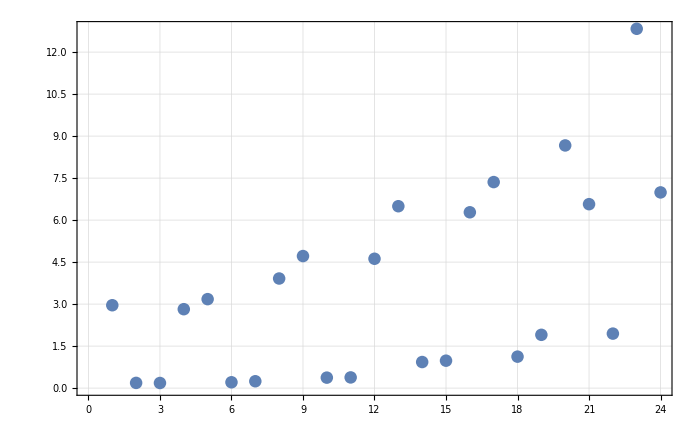

```mathematica
ListPlot[testBinInt[[All,1]]/3600]
```

```mathematica
testBinCenters=BinCenters[XY24BinsXOff]
```

{{-0.025,-0.015},{-0.025,-0.005},{-0.025,0.005},{-0.025,0.015},{-0.015,-0.015},{-0.015,-0.005},{-0.015,0.005},{-0.015,0.015},{-0.005,-0.015},{-0.005,-0.005},{-0.005,0.005},{-0.005,0.015},{0.005,-0.015},{0.005,-0.005},{0.005,0.005},{0.005,0.015},{0.015,-0.015},{0.015,-0.005},{0.015,0.005},{0.015,0.015},{0.025,-0.015},{0.025,-0.005},{0.025,0.005},{0.025,0.015}}

```mathematica
Show[
ListPlot3D[Transpose[{testBinCenters[[All,1]],testBinCenters[[All,2]],testBinInt[[All,2]]}],InterpolationOrder->1],
ParametricPlot3D[{{xD,-0.035/2,0.},{xD,0.035/2,0.}},{xD,-0.03-0.005,-0.03+0.005},PlotStyle->Red],
ParametricPlot3D[{{-0.03-0.005,yD,0.},{-0.03+0.005,yD,0.}},{yD,-0.035/2,0.035/2},PlotStyle->Red]
]
```

-Graphics3D-

```mathematica
Show[
ListPlot3D[Transpose[{testBinCenters[[All,1]],testBinCenters[[All,2]],testBinInt[[All,1]]/3600}]],
ParametricPlot3D[{{xD,-0.035/2,0.},{xD,0.035/2,0.}},{xD,-0.03-0.005,-0.03+0.005},PlotStyle->Red],
ParametricPlot3D[{{-0.03-0.005,yD,0.},{-0.03+0.005,yD,0.}},{yD,-0.035/2,0.035/2},PlotStyle->Red]
]
```

-Graphics3D-

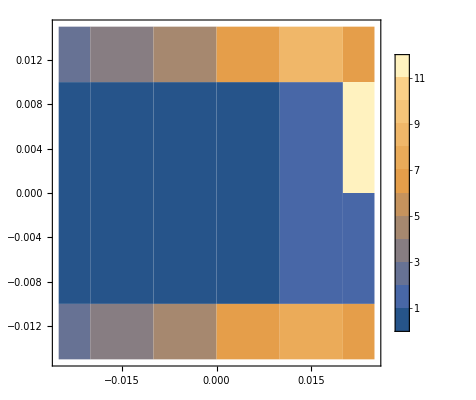

```mathematica
ListContourPlot[Transpose[{testBinCenters[[All,1]],testBinCenters[[All,2]],testBinInt[[All,1]]/3600}],Contours->11,PlotLegends->Automatic,InterpolationOrder->0]
```

## Now Full spectrum with reduced accuracy

```mathematica
XY35BinsXOff=XYBinIntBoundaries[{-0.005,0.065,-0.03,7},{-0.02,0.02,0.,5}]
```

{{{-0.035,-0.025},{-0.02,-0.012}},{{-0.035,-0.025},{-0.012,-0.004}},{{-0.035,-0.025},{-0.004,0.004}},{{-0.035,-0.025},{0.004,0.012}},{{-0.035,-0.025},{0.012,0.02}},{{-0.025,-0.015},{-0.02,-0.012}},{{-0.025,-0.015},{-0.012,-0.004}},{{-0.025,-0.015},{-0.004,0.004}},{{-0.025,-0.015},{0.004,0.012}},{{-0.025,-0.015},{0.012,0.02}},{{-0.015,-0.005},{-0.02,-0.012}},{{-0.015,-0.005},{-0.012,-0.004}},{{-0.015,-0.005},{-0.004,0.004}},{{-0.015,-0.005},{0.004,0.012}},{{-0.015,-0.005},{0.012,0.02}},{{-0.005,0.005},{-0.02,-0.012}},{{-0.005,0.005},{-0.012,-0.004}},{{-0.005,0.005},{-0.004,0.004}},{{-0.005,0.005},{0.004,0.012}},{{-0.005,0.005},{0.012,0.02}},{{0.005,0.015},{-0.02,-0.012}},{{0.005,0.015},{-0.012,-0.004}},{{0.005,0.015},{-0.004,0.004}},{{0.005,0.015},{0.004,0.012}},{{0.005,0.015},{0.012,0.02}},{{0.015,0.025},{-0.02,-0.012}},{{0.015,0.025},{-0.012,-0.004}},{{0.015,0.025},{-0.004,0.004}},{{0.015,0.025},{0.004,0.012}},{{0.015,0.025},{0.012,0.02}},{{0.025,0.035},{-0.02,-0.012}},{{0.025,0.035},{-0.012,-0.004}},{{0.025,0.035},{-0.004,0.004}},{{0.025,0.035},{0.004,0.012}},{{0.025,0.035},{0.012,0.02}}}

```mathematica
BinCentersXY35BinsXOff=BinCenters[XY35BinsXOff]
```

{{-0.03,-0.016},{-0.03,-0.008},{-0.03,0.},{-0.03,0.008},{-0.03,0.016},{-0.02,-0.016},{-0.02,-0.008},{-0.02,0.},{-0.02,0.008},{-0.02,0.016},{-0.01,-0.016},{-0.01,-0.008},{-0.01,0.},{-0.01,0.008},{-0.01,0.016},{3.46945×10^-18,-0.016},{3.46945×10^-18,-0.008},{3.46945×10^-18,0.},{3.46945×10^-18,0.008},{3.46945×10^-18,0.016},{0.01,-0.016},{0.01,-0.008},{0.01,0.},{0.01,0.008},{0.01,0.016},{0.02,-0.016},{0.02,-0.008},{0.02,0.},{0.02,0.008},{0.02,0.016},{0.03,-0.016},{0.03,-0.008},{0.03,0.},{0.03,0.008},{0.03,0.016}}

```mathematica
CloseKernels[]
LaunchKernels[]
```

{}

{KernelObject[1,192.168.0.220],KernelObject[2,192.168.0.220],KernelObject[3,192.168.0.220],KernelObject[4,192.168.0.220],KernelObject[5,192.168.0.220],KernelObject[6,192.168.0.220],KernelObject[7,192.168.0.150],KernelObject[8,192.168.0.150],KernelObject[9,192.168.0.150],KernelObject[10,local],KernelObject[11,local],KernelObject[12,local]}

```mathematica
?BinInt
```

```mathematica
BinInt35Bins=ParallelMap[
(BinInt[0.,#,{Pi,0.2,2.,1.,1.,1.,1.,1.,1.},{0.06,0.05,0.9,0.,-0.9,0.1,0.09,0.9,0.,-0.9},{0.01,0.035,-0.03,0.},
{IntOptionList[[6]],3,3,0,2},{IntOptionList[[6]],3,3,0,2},{IntOptionList[[6]],3,4}
]//AbsoluteTiming
)&,XY35BinsXOff,Method->"FinestGrained"]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {-0.0165588,-0.0163118}. NIntegrate obtained 0.0639072 and 0.000100722 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {0.00344124,0.0196882}. NIntegrate obtained 0.187906 and 0.000307258 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {0.00344124,-0.0163118}. NIntegrate obtained 0.191909 and 0.000246036 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {0.0134412,-0.0183118}. NIntegrate obtained 0.153528 and 0.000153802 for the integral and error estimates.

{{662.946,0.00584441},{155.145,0.00829889},{150.89,0.00809271},{150.69,0.00789359},{729.322,0.00533333},{7330.19,0.0639072},{233.347,0.0940088},{193.196,0.0920083},{268.891,0.0898493},{7840.67,0.0589808},{9504.89,0.154314},{575.053,0.236304},{195.484,0.236329},{573.512,0.228881},{8169.26,0.145871},{15499.1,0.191909},{869.263,0.296409},{311.435,0.310367},{969.075,0.293396},{14144.6,0.187906},{16744.5,0.153528},{2030.86,0.235889},{1116.25,0.257148},{1945.4,0.239517},{12802.8,0.157493},{2398.36,0.0807423},{1635.41,0.124692},{2305.09,0.139243},{1912.42,0.130545},{2080.78,0.0882625},{1738.27,0.0259767},{2597.32,0.0404676},{2314.93,0.0469157},{2048.84,0.0442835},{1690.82,0.0307095}}

```mathematica
BinInt35BinsOld={{662.9462147342865,0.0058444098516682455},{155.14473057803306,0.008298889536430012},{150.8902887598839,0.008092712124922968},{150.69024557999634,0.007893585948520793},{729.321765550534,0.005333333996789096},{7330.1851637627715,0.06390719911669854},{233.3470917707129,0.0940087719229084},{193.1958133491687,0.0920082824949},{268.891090150549,0.08984928122494204},{7840.665325,0.0589807674503259},{9504.889048,0.15431393706715835},{575.053452,0.2363043861903529},{195.4836638230818,0.236328904627502},{573.5118741482719,0.22888072807534704},{8169.257014646515,0.1458707713109207},{15499.13107926763,0.19190936646349982},{869.2628467542365,0.29640873629749814},{311.4346343935315,0.31036717204501907},{969.0745699976133,0.2933963624274661},{14144.60988,0.18790597257681868},{16744.51675572113,0.15352826815817874},{2030.8581197436667,0.23588852378359437},{1116.2535855988338,0.2571479698936176},{1945.396827336911,0.2395169423600201},{12802.77619820239,0.15749294296332142},{2398.358063282595,0.08074230791930542},{1635.4098797892461,0.12469198843791961},{2305.0928694799677,0.13924250374804928},{1912.4223535156,0.13054544726026213},{2080.779641100067,0.08826254906410953},{1738.2658899419735,0.025976675373192187},{2597.317847922104,0.04046758951797638},{2314.9301544466944,0.04691574974374615},{2048.8375708009003,0.04428347260603145},{1690.8181385683013,0.030709504202892784}};
```

```mathematica
CloseKernels[]
```

{}

```mathematica
LaunchKernels[]
```

{KernelObject[1,193.170.93.93],KernelObject[2,193.170.93.93],KernelObject[3,193.170.93.93],KernelObject[4,193.170.93.93],KernelObject[5,193.170.93.93],KernelObject[6,193.170.93.93],KernelObject[7,193.170.93.100],KernelObject[8,193.170.93.100],KernelObject[9,193.170.93.100],KernelObject[10,193.170.93.100],KernelObject[11,local],KernelObject[12,local],KernelObject[13,local],KernelObject[14,local]}

```mathematica
BinInt35Bins=ParallelMap[
(BinInt[0.,#,{Pi,0.2,2.,1.,1.,1.,1.,1.,1.},{0.06,0.05,0.9,0.,-0.9,0.1,0.09,0.9,0.,-0.9},{0.01,0.035,-0.03,0.},
{IntOptionList[[6]],3,3,2,3},{IntOptionList[[6]],3,3,0,2},{IntOptionList[[6]],3,4}
]//AbsoluteTiming
)&,XY35BinsXOff,Method->"FinestGrained"]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {0.00344124,0.0196882}. NIntegrate obtained 0.187913 and 0.00021942 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {-0.0165588,-0.0163118}. NIntegrate obtained 0.0639053 and 0.000101554 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {0.00344124,-0.0163118}. NIntegrate obtained 0.19191 and 0.000248866 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {0.0134412,-0.0183118}. NIntegrate obtained 0.153525 and 0.000169011 for the integral and error estimates.

{{3874.87,0.00584446},{1635.2,0.00829882},{1647.85,0.00809265},{1658.14,0.00789353},{4520.98,0.00533355},{51858.5,0.0639053},{2093.93,0.0940087},{1878.34,0.0920079},{2211.9,0.089849},{33012.7,0.0589798},{60772.5,0.154322},{4397.68,0.236296},{2528.15,0.236329},{4554.92,0.228878},{54921.2,0.145876},{95437.6,0.19191},{6913.64,0.296394},{2042.45,0.310362},{4272.48,0.293424},{39567.1,0.187913},{106907.,0.153525},{10560.8,0.235884},{4619.31,0.257148},{11232.5,0.239514},{75493.5,0.157504},{13305.1,0.0807473},{19137.2,0.12434},{7719.48,0.139237},{10106.,0.130545},{11201.,0.0882717},{8436.97,0.0259767},{7153.38,0.0404653},{10535.,0.0469175},{9563.43,0.0442827},{5210.15,0.0307094}}

```mathematica
ListPlot3D[Transpose[{BinCentersXY35BinsXOff[[All,1]],BinCentersXY35BinsXOff[[All,2]],(BinInt35Bins[[All,2]]-BinInt35BinsOld[[All,2]])/BinInt35Bins[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### took 17325s, 4.8h

```mathematica
BinCenters35=BinCenters[XY35BinsXOff]
```

{{-0.03,-0.016},{-0.03,-0.008},{-0.03,0.},{-0.03,0.008},{-0.03,0.016},{-0.02,-0.016},{-0.02,-0.008},{-0.02,0.},{-0.02,0.008},{-0.02,0.016},{-0.01,-0.016},{-0.01,-0.008},{-0.01,0.},{-0.01,0.008},{-0.01,0.016},{3.46945×10^-18,-0.016},{3.46945×10^-18,-0.008},{3.46945×10^-18,0.},{3.46945×10^-18,0.008},{3.46945×10^-18,0.016},{0.01,-0.016},{0.01,-0.008},{0.01,0.},{0.01,0.008},{0.01,0.016},{0.02,-0.016},{0.02,-0.008},{0.02,0.},{0.02,0.008},{0.02,0.016},{0.03,-0.016},{0.03,-0.008},{0.03,0.},{0.03,0.008},{0.03,0.016}}

```mathematica
Show[
ListPlot3D[Transpose[{BinCenters35[[All,1]],BinCenters35[[All,2]],BinInt35Bins[[All,2]]}],InterpolationOrder->1],
ParametricPlot3D[{{xD,-0.035/2,0.},{xD,0.035/2,0.}},{xD,-0.03-0.005,-0.03+0.005},PlotStyle->Red],
ParametricPlot3D[{{-0.03-0.005,yD,0.},{-0.03+0.005,yD,0.}},{yD,-0.035/2,0.035/2},PlotStyle->Red]
]
```

-Graphics3D-

```mathematica
Show[
ListPlot3D[Transpose[{BinCenters35[[All,1]],BinCenters35[[All,2]],BinInt35Bins[[All,1]]/3600}],PlotRange->All],
ParametricPlot3D[{{xD,-0.035/2,0.},{xD,0.035/2,0.}},{xD,-0.03-0.005,-0.03+0.005},PlotStyle->Red],
ParametricPlot3D[{{-0.03-0.005,yD,0.},{-0.03+0.005,yD,0.}},{yD,-0.035/2,0.035/2},PlotStyle->Red]
]
```

-Graphics3D-

# BRxB Variation

## 0.2 T

```mathematica
BinInt35BinsBVary1=ParallelMap[
(BinInt[-0.001,#,{Pi,0.2+0.2*5*10^-5,2.,1.,1.,1.,1.,1.,1.},{0.06,0.05,0.9,0.,-0.9,0.1,0.09,0.9,0.,-0.9},{0.01,0.035,-0.03,0.},
{IntOptionList[[6]],3,3,0,2},{IntOptionList[[6]],3,3,0,2},{IntOptionList[[6]],3,4}
]//AbsoluteTiming
)&,XY35BinsXOff,Method->"FinestGrained"]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {-0.0165588,-0.0163118}. NIntegrate obtained 0.0639007 and 0.000100714 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {0.00344124,0.0196882}. NIntegrate obtained 0.187915 and 0.000307273 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {0.00344124,-0.0163118}. NIntegrate obtained 0.191919 and 0.000246073 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {0.0134412,-0.0183118}. NIntegrate obtained 0.153536 and 0.000153826 for the integral and error estimates.

{{671.359,0.0058434},{158.397,0.00829745},{152.618,0.00809131},{151.372,0.00789221},{738.61,0.0053324},{7340.14,0.0639007},{260.613,0.0939992},{215.431,0.0919988},{299.448,0.0898399},{7843.58,0.0589745},{9521.73,0.154312},{568.395,0.236302},{195.294,0.236326},{573.432,0.228877},{8194.94,0.145868},{15828.6,0.191919},{957.053,0.296423},{340.885,0.310382},{976.408,0.29341},{14085.9,0.187915},{16851.1,0.153536},{2041.31,0.235901},{1124.77,0.257161},{1944.66,0.23953},{13278.9,0.157502},{2409.91,0.0807406},{1644.88,0.12469},{2300.62,0.139241},{1923.,0.130544},{2094.24,0.0882619},{1749.68,0.0259723},{2607.06,0.0404612},{2318.08,0.0469086},{2029.92,0.0442768},{1698.95,0.0307048}}

```mathematica
Print[DateString[]]
BinInt35BinsBVary2=ParallelMap[
(BinInt[-0.0015,#,{Pi,0.2+0.2*5*10^-5,2.,1.,1.,1.,1.,1.,1.},{0.06,0.05,0.9,0.,-0.9,0.1,0.09,0.9,0.,-0.9},{0.01,0.035,-0.03,0.},
{IntOptionList[[6]],3,3,0,2},{IntOptionList[[6]],3,3,0,2},{IntOptionList[[6]],3,4}
]//AbsoluteTiming
)&,XY35BinsXOff,Method->"FinestGrained"]
```

Sun 29 Mar 2020 00:59:33

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {-0.0165588,-0.0163118}. NIntegrate obtained 0.0638933 and 0.000100702 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {0.00344124,-0.0163118}. NIntegrate obtained 0.191919 and 0.000246063 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {0.00344124,0.0196882}. NIntegrate obtained 0.187914 and 0.000307284 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {0.0134412,-0.0183118}. NIntegrate obtained 0.153543 and 0.000153833 for the integral and error estimates.

{{671.759,0.00584249},{158.928,0.00829615},{153.682,0.00809004},{152.657,0.00789097},{737.722,0.00533156},{7359.19,0.0638933},{234.639,0.0939883},{194.53,0.0919881},{270.814,0.0898293},{7853.89,0.0589675},{9529.73,0.154303},{568.63,0.236288},{196.991,0.236312},{576.42,0.228864},{8190.65,0.145859},{14395.2,0.191919},{864.857,0.296423},{309.838,0.310382},{976.053,0.293409},{14126.8,0.187914},{15458.5,0.153543},{2044.6,0.23591},{1123.96,0.257172},{1955.44,0.239539},{11908.6,0.157508},{2408.36,0.0807463},{1641.23,0.124699},{2308.02,0.139251},{1916.63,0.130553},{2105.49,0.0882679},{1755.64,0.0259746},{2582.93,0.0404648},{2327.95,0.0469127},{2043.88,0.0442806},{1710.55,0.0307075}}

### took 16039s, 4.5h

```mathematica
Print[DateString[]]
BinInt35BinsBVary3=ParallelMap[
(BinInt[-0.0005,#,{Pi,0.2+0.2*5*10^-5,2.,1.,1.,1.,1.,1.,1.},{0.06,0.05,0.9,0.,-0.9,0.1,0.09,0.9,0.,-0.9},{0.01,0.035,-0.03,0.},
{IntOptionList[[6]],3,3,0,2},{IntOptionList[[6]],3,3,0,2},{IntOptionList[[6]],3,4}
]//AbsoluteTiming
)&,XY35BinsXOff,Method->"FinestGrained"]
```

Sun 29 Mar 2020 22:59:13

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {-0.0165588,-0.0163118}. NIntegrate obtained 0.0639081 and 0.000100725 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {0.00344124,0.0196882}. NIntegrate obtained 0.187916 and 0.000307273 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {0.00344124,-0.0163118}. NIntegrate obtained 0.191919 and 0.00024605 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {0.0134412,-0.0183118}. NIntegrate obtained 0.15353 and 0.000153818 for the integral and error estimates.

{{668.15,0.00584431},{156.974,0.00829875},{155.021,0.00809258},{154.333,0.00789345},{740.087,0.00533324},{7374.96,0.0639081},{286.394,0.0940101},{237.961,0.0920095},{328.387,0.0898504},{7866.42,0.0589815},{9519.52,0.154321},{569.33,0.236315},{198.31,0.236339},{577.085,0.228891},{8174.97,0.145877},{14460.1,0.191919},{890.323,0.296423},{322.126,0.310383},{979.424,0.293411},{14081.2,0.187916},{15518.5,0.15353},{2032.35,0.235891},{1133.92,0.257151},{1960.4,0.239521},{11956.7,0.157495},{2427.96,0.0807349},{1656.53,0.124681},{2304.75,0.139232},{1910.03,0.130535},{2113.96,0.0882559},{1761.94,0.02597},{2587.87,0.0404577},{2321.28,0.0469046},{2045.31,0.0442729},{1713.75,0.0307021}}

```mathematica
Print[DateString[]]
BinInt35BinsBVary4=ParallelMap[
(BinInt[-0.002,#,{Pi,0.2+0.2*5*10^-5,2.,1.,1.,1.,1.,1.,1.},{0.06,0.05,0.9,0.,-0.9,0.1,0.09,0.9,0.,-0.9},{0.01,0.035,-0.03,0.},
{IntOptionList[[6]],3,3,0,2},{IntOptionList[[6]],3,3,0,2},{IntOptionList[[6]],3,4}
]//AbsoluteTiming
)&,XY35BinsXOff,Method->"FinestGrained"]
```

Mon 30 Mar 2020 03:28:43

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {-0.0165588,-0.0163118}. NIntegrate obtained 0.0638859 and 0.000100691 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {0.00344124,-0.0163118}. NIntegrate obtained 0.191919 and 0.000246102 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {0.00344124,0.0196882}. NIntegrate obtained 0.187913 and 0.000307284 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {0.0134412,-0.0183118}. NIntegrate obtained 0.153549 and 0.000153838 for the integral and error estimates.

{{667.849,0.00584157},{158.428,0.00829485},{153.84,0.00808876},{153.133,0.00788973},{741.458,0.00533072},{7368.75,0.0638859},{235.546,0.0939774},{195.357,0.0919773},{272.214,0.0898188},{7856.75,0.0589605},{9507.9,0.154295},{566.948,0.236275},{197.842,0.236299},{582.643,0.22885},{8187.03,0.145851},{14419.5,0.191919},{868.492,0.296422},{311.456,0.310381},{983.977,0.293408},{14051.6,0.187913},{15509.8,0.153549},{2049.26,0.23592},{1134.77,0.257182},{1957.83,0.239548},{11956.2,0.157514},{2430.08,0.080752},{1659.92,0.124708},{2309.49,0.13926},{1915.36,0.130562},{2108.47,0.0882739},{1758.26,0.0259768},{2591.32,0.0404683},{2327.2,0.0469168},{2037.5,0.0442844},{1704.22,0.0307101}}

```mathematica
bList={-0.001,-0.0015,-0.0005,-0.002};
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

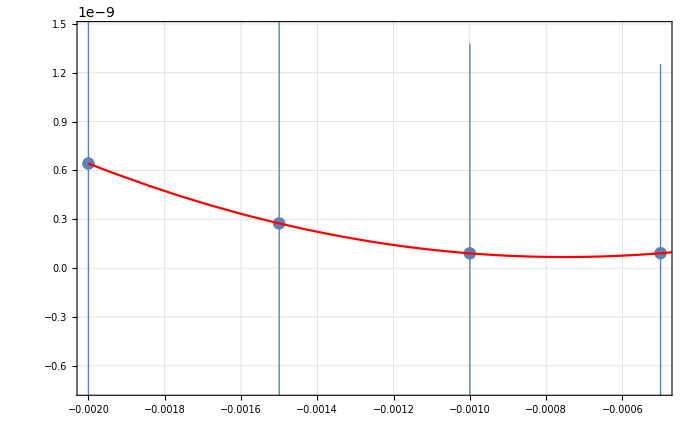
{b0 =  | -0.000752317
FittedModel[6.82843×10^-11+0.00036908 (0.000752317+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.000752317 | 0.00417002 | -0.180411 | 0.886369
scale | 0.00036908 | 0.00356047 | 0.10366 | 0.934243
yoffset | 6.82843×10^-11 | 9.10762×10^-10 | 0.0749749 | 0.952359 | 
 | DF | SS | MS
Model | 3 | 0.0733796 | 0.0244599
Error | 1 | 8.38924×10^-9 | 8.38924×10^-9
Uncorrected Total | 4 | 0.0733796 | 
Corrected Total | 3 | 0.034434 |  | ,-Graphics-}

```mathematica
testfit=Chi2FitandPlot[BinInt35Bins[[All,2]]/Total[BinInt35Bins[[All,2]]],{BinInt35BinsBVary1/Total[BinInt35BinsBVary1[[All,2]]],BinInt35BinsBVary2/Total[BinInt35BinsBVary2[[All,2]]],BinInt35BinsBVary3/Total[BinInt35BinsBVary3[[All,2]]],BinInt35BinsBVary4/Total[BinInt35BinsBVary4[[All,2]]]},bList,3]
```

```mathematica
testfit[[1,1,1,2]]/(5*10^-5)
```

-15.0463

## All BRxB Ramp

## 1T

```mathematica
XY35BinsBRamp[[7]]
```

{{{-0.005,-0.00157143},{-0.02,-0.012}},{{-0.005,-0.00157143},{-0.012,-0.004}},{{-0.005,-0.00157143},{-0.004,0.004}},{{-0.005,-0.00157143},{0.004,0.012}},{{-0.005,-0.00157143},{0.012,0.02}},{{-0.00157143,0.00185714},{-0.02,-0.012}},{{-0.00157143,0.00185714},{-0.012,-0.004}},{{-0.00157143,0.00185714},{-0.004,0.004}},{{-0.00157143,0.00185714},{0.004,0.012}},{{-0.00157143,0.00185714},{0.012,0.02}},{{0.00185714,0.00528571},{-0.02,-0.012}},{{0.00185714,0.00528571},{-0.012,-0.004}},{{0.00185714,0.00528571},{-0.004,0.004}},{{0.00185714,0.00528571},{0.004,0.012}},{{0.00185714,0.00528571},{0.012,0.02}},{{0.00528571,0.00871429},{-0.02,-0.012}},{{0.00528571,0.00871429},{-0.012,-0.004}},{{0.00528571,0.00871429},{-0.004,0.004}},{{0.00528571,0.00871429},{0.004,0.012}},{{0.00528571,0.00871429},{0.012,0.02}},{{0.00871429,0.0121429},{-0.02,-0.012}},{{0.00871429,0.0121429},{-0.012,-0.004}},{{0.00871429,0.0121429},{-0.004,0.004}},{{0.00871429,0.0121429},{0.004,0.012}},{{0.00871429,0.0121429},{0.012,0.02}},{{0.0121429,0.0155714},{-0.02,-0.012}},{{0.0121429,0.0155714},{-0.012,-0.004}},{{0.0121429,0.0155714},{-0.004,0.004}},{{0.0121429,0.0155714},{0.004,0.012}},{{0.0121429,0.0155714},{0.012,0.02}},{{0.0155714,0.019},{-0.02,-0.012}},{{0.0155714,0.019},{-0.012,-0.004}},{{0.0155714,0.019},{-0.004,0.004}},{{0.0155714,0.019},{0.004,0.012}},{{0.0155714,0.019},{0.012,0.02}}}

```mathematica
CloseKernels[]
```

{KernelObject[1,192.168.0.220,<defunct>],KernelObject[2,192.168.0.220,<defunct>],KernelObject[3,192.168.0.220,<defunct>],KernelObject[4,192.168.0.220,<defunct>],KernelObject[5,192.168.0.220,<defunct>],KernelObject[6,192.168.0.220,<defunct>],KernelObject[7,192.168.0.150,<defunct>],KernelObject[8,192.168.0.150,<defunct>],KernelObject[9,192.168.0.150,<defunct>],KernelObject[10,local,<defunct>],KernelObject[11,local,<defunct>],KernelObject[12,local,<defunct>]}

```mathematica
LaunchKernels[]
```

{KernelObject[13,192.168.0.220],KernelObject[14,192.168.0.220],KernelObject[15,192.168.0.220],KernelObject[16,192.168.0.220],KernelObject[17,192.168.0.150],KernelObject[18,192.168.0.150],KernelObject[19,local],KernelObject[20,local],KernelObject[21,local]}

```mathematica
BinInt35Bins1000=ParallelMap[
(BinInt[0.,#,{Pi,BRxBList[[7]],2.,1.,1.,1.,1.,1.,1.},{0.06,0.05,0.9,0.,-0.9,0.1,0.09,0.9,0.,-0.9},{0.01,0.035,0.,0.},
{IntOptionList[[6]],4,3,0,2},{IntOptionList[[6]],3,3,0,2},{IntOptionList[[6]],3,4}
]//AbsoluteTiming
)&,XY35BinsXOffBRamp[[7]],Method->"FinestGrained"]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {0.00132271,-0.0163118}. NIntegrate obtained 0.0884743 and 0.000391695 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {0.00132271,0.0176882}. NIntegrate obtained 0.0828587 and 0.000387018 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {0.00817985,-0.0163118}. NIntegrate obtained 0.242575 and 0.000628065 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {0.00475128,-0.0163118}. NIntegrate obtained 0.203574 and 0.000648312 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {0.00475128,0.0176882}. NIntegrate obtained 0.197161 and 0.000618772 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {0.00817985,0.0176882}. NIntegrate obtained 0.241782 and 0.000628419 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {0.0116084,-0.0163118}. NIntegrate obtained 0.162888 and 0.00031458 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {0.0116084,0.0176882}. NIntegrate obtained 0.168783 and 0.000343227 for the integral and error estimates.

{{2915.47,0.00883379},{470.56,0.0126022},{509.621,0.0123035},{506.193,0.0120142},{2920.06,0.00808863},{4851.83,0.0884743},{491.181,0.126775},{499.787,0.124537},{517.326,0.122342},{5275.18,0.0828587},{6969.64,0.203574},{316.292,0.294228},{250.791,0.291688},{280.576,0.289128},{7684.64,0.197161},{6188.78,0.242575},{98.5894,0.352955},{104.041,0.352664},{88.9786,0.352329},{7858.96,0.241782},{7803.74,0.162888},{280.446,0.239705},{261.081,0.242053},{263.861,0.244356},{8219.12,0.168783},{1727.86,0.0509802},{594.07,0.0764846},{577.851,0.0789003},{485.365,0.0813809},{1901.84,0.0570974},{973.457,0.00571116},{676.817,0.00884581},{680.936,0.00942825},{681.535,0.0100392},{950.358,0.00720694}}

### took ~11000s, 3h

```mathematica
ListPlot3D[Transpose[{BinCentersBRamp[[7,All,1]],BinCentersBRamp[[7,All,2]],BinInt35Bins1000[[All,2]]}]]
```

-Graphics3D-

```mathematica
BinInt35Bins1000bvary1=ParallelMap[
(BinInt[-0.0015,#,{Pi,BRxBList[[7]]+BRxBList[[7]]*5*10^-5,2.,1.,1.,1.,1.,1.,1.},{0.06,0.05,0.9,0.,-0.9,0.1,0.09,0.9,0.,-0.9},{0.01,0.035,0.,0.},
{IntOptionList[[6]],4,3,0,2},{IntOptionList[[6]],3,3,0,2},{IntOptionList[[6]],3,4}
]//AbsoluteTiming
)&,XY35BinsXOffBRamp[[7]],Method->"FinestGrained"]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {0.00132271,-0.0163118}. NIntegrate obtained 0.0884657 and 0.00039163 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {0.00132271,0.0176882}. NIntegrate obtained 0.0828501 and 0.000386958 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {0.00817985,-0.0163118}. NIntegrate obtained 0.242579 and 0.000628035 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {0.00475128,-0.0163118}. NIntegrate obtained 0.203572 and 0.000648348 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {0.00475128,0.0176882}. NIntegrate obtained 0.197159 and 0.00061852 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {0.00817985,0.0176882}. NIntegrate obtained 0.241786 and 0.000628586 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {0.0116084,-0.0163118}. NIntegrate obtained 0.162897 and 0.000314606 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {0.0116084,0.0176882}. NIntegrate obtained 0.168791 and 0.000343236 for the integral and error estimates.

{{3291.76,0.00883148},{555.528,0.0125989},{514.742,0.0123002},{510.124,0.012011},{2943.33,0.00808646},{4907.76,0.0884657},{487.432,0.126762},{494.599,0.124525},{511.486,0.12233},{6145.65,0.0828501},{6997.82,0.203572},{259.565,0.294226},{300.468,0.291685},{280.753,0.289126},{7122.36,0.197159},{6234.58,0.242579},{98.557,0.352961},{104.593,0.35267},{89.0534,0.352335},{7861.34,0.241786},{7993.06,0.162897},{269.604,0.239717},{262.353,0.242066},{290.03,0.244369},{7525.42,0.168791},{1898.81,0.0509809},{612.808,0.0764852},{649.78,0.0789016},{490.602,0.0813824},{1778.57,0.0570986},{1081.2,0.00571012},{834.945,0.00884423},{698.176,0.00942661},{759.716,0.0100375},{1201.54,0.00720576}}

```mathematica
CloseKernels[]
LaunchKernels[]
```

{KernelObject[13,192.168.0.220,<defunct>],KernelObject[14,192.168.0.220,<defunct>],KernelObject[15,192.168.0.220,<defunct>],KernelObject[16,192.168.0.220,<defunct>],KernelObject[17,192.168.0.150,<defunct>],KernelObject[18,192.168.0.150,<defunct>],KernelObject[19,local,<defunct>],KernelObject[20,local,<defunct>],KernelObject[21,local,<defunct>]}

{KernelObject[22,192.168.0.220],KernelObject[23,192.168.0.220],KernelObject[24,192.168.0.220],KernelObject[25,192.168.0.220],KernelObject[26,192.168.0.220],KernelObject[27,192.168.0.220],KernelObject[28,192.168.0.150],KernelObject[29,192.168.0.150],KernelObject[30,192.168.0.150],KernelObject[31,local],KernelObject[32,local],KernelObject[33,local]}

```mathematica
BinInt35Bins1000bvary2=ParallelMap[
(BinInt[-0.001,#,{Pi,BRxBList[[7]]+BRxBList[[7]]*5*10^-5,2.,1.,1.,1.,1.,1.,1.},{0.06,0.05,0.9,0.,-0.9,0.1,0.09,0.9,0.,-0.9},{0.01,0.035,0.,0.},
{IntOptionList[[6]],4,3,0,2},{IntOptionList[[6]],3,3,0,2},{IntOptionList[[6]],3,4}
]//AbsoluteTiming
)&,XY35BinsXOffBRamp[[7]],Method->"FinestGrained"]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {0.00132271,-0.0163118}. NIntegrate obtained 0.0884716 and 0.000391661 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {0.00132271,0.0176882}. NIntegrate obtained 0.0828559 and 0.000386993 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {0.00817985,-0.0163118}. NIntegrate obtained 0.242578 and 0.000628052 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {0.00475128,0.0176882}. NIntegrate obtained 0.197164 and 0.000618756 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {0.00475128,-0.0163118}. NIntegrate obtained 0.203577 and 0.000648385 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {0.00817985,0.0176882}. NIntegrate obtained 0.241786 and 0.000628604 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {0.0116084,-0.0163118}. NIntegrate obtained 0.162891 and 0.0003146 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {0.0116084,0.0176882}. NIntegrate obtained 0.168786 and 0.00034323 for the integral and error estimates.

{{2992.19,0.00883265},{497.694,0.0126006},{497.694,0.0123018},{558.548,0.0120126},{3262.15,0.00808755},{5287.97,0.0884716},{437.5,0.126771},{443.711,0.124533},{465.45,0.122338},{6187.92,0.0828559},{6994.17,0.203577},{305.483,0.294232},{301.743,0.291691},{299.775,0.289132},{6546.25,0.197164},{6381.6,0.242578},{97.511,0.35296},{86.4645,0.352669},{97.2255,0.352334},{6547.51,0.241786},{7946.77,0.162891},{326.353,0.239708},{289.846,0.242057},{286.939,0.24436},{9515.73,0.168786},{1942.66,0.0509772},{665.323,0.0764797},{627.176,0.078896},{534.1,0.0813766},{1937.22,0.0570946},{1086.44,0.00570958},{696.178,0.00884339},{769.828,0.00942572},{692.164,0.0100365},{1021.48,0.00720508}}

```mathematica
BinInt35Bins1000bvary3=ParallelMap[
(BinInt[-0.0005,#,{Pi,BRxBList[[7]]+BRxBList[[7]]*5*10^-5,2.,1.,1.,1.,1.,1.,1.},{0.06,0.05,0.9,0.,-0.9,0.1,0.09,0.9,0.,-0.9},{0.01,0.035,0.,0.},
{IntOptionList[[6]],4,3,0,2},{IntOptionList[[6]],3,3,0,2},{IntOptionList[[6]],3,4}
]//AbsoluteTiming
)&,XY35BinsXOffBRamp[[7]],Method->"FinestGrained"]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {0.00132271,-0.0163118}. NIntegrate obtained 0.0884775 and 0.000391705 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {0.00132271,0.0176882}. NIntegrate obtained 0.0828617 and 0.000387024 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {0.00817985,-0.0163118}. NIntegrate obtained 0.242577 and 0.000628081 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {0.00475128,-0.0163118}. NIntegrate obtained 0.203581 and 0.000648423 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {0.00475128,0.0176882}. NIntegrate obtained 0.197168 and 0.000618792 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {0.00817985,0.0176882}. NIntegrate obtained 0.241785 and 0.000628429 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {0.0116084,-0.0163118}. NIntegrate obtained 0.162885 and 0.000314592 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {0.0116084,0.0176882}. NIntegrate obtained 0.16878 and 0.000343226 for the integral and error estimates.

{{3011.02,0.00883381},{506.961,0.0126022},{506.794,0.0123035},{568.852,0.0120142},{3272.08,0.00808864},{5306.76,0.0884775},{439.684,0.126779},{456.646,0.124542},{477.92,0.122347},{6186.21,0.0828617},{6993.23,0.203581},{309.822,0.294238},{300.744,0.291698},{300.82,0.289138},{6561.46,0.197168},{6389.94,0.242577},{97.8886,0.352959},{86.9764,0.352668},{98.2499,0.352333},{6641.26,0.241785},{8039.85,0.162885},{324.956,0.239699},{292.32,0.242048},{288.499,0.244352},{9497.31,0.16878},{1945.2,0.0509736},{659.224,0.0764748},{626.73,0.0788903},{536.655,0.0813709},{1938.3,0.0570906},{1095.98,0.00570904},{699.562,0.00884256},{773.755,0.00942483},{697.168,0.0100356},{1028.58,0.0072044}}

```mathematica
BinInt35Bins1000bvary4=ParallelMap[
(BinInt[-0.00,#,{Pi,BRxBList[[7]]+BRxBList[[7]]*5*10^-5,2.,1.,1.,1.,1.,1.,1.},{0.06,0.05,0.9,0.,-0.9,0.1,0.09,0.9,0.,-0.9},{0.01,0.035,0.,0.},
{IntOptionList[[6]],4,3,0,2},{IntOptionList[[6]],3,3,0,2},{IntOptionList[[6]],3,4}
]//AbsoluteTiming
)&,XY35BinsXOffBRamp[[7]],Method->"FinestGrained"]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {0.00132271,-0.0163118}. NIntegrate obtained 0.0884834 and 0.000391736 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {0.00132271,0.0176882}. NIntegrate obtained 0.0828675 and 0.00038706 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {0.00817985,-0.0163118}. NIntegrate obtained 0.242576 and 0.000629177 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {0.00475128,-0.0163118}. NIntegrate obtained 0.203585 and 0.000648396 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {0.00475128,0.0176882}. NIntegrate obtained 0.197172 and 0.000618828 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {0.00817985,0.0176882}. NIntegrate obtained 0.241785 and 0.000628447 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {0.0116084,-0.0163118}. NIntegrate obtained 0.162879 and 0.000314586 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {0.0116084,0.0176882}. NIntegrate obtained 0.168774 and 0.000343221 for the integral and error estimates.

{{3011.3,0.00883498},{507.417,0.0126039},{509.026,0.0123051},{570.592,0.0120158},{3276.38,0.00808972},{5278.03,0.0884834},{440.444,0.126788},{458.346,0.12455},{479.041,0.122355},{6186.34,0.0828675},{6977.56,0.203585},{309.075,0.294244},{300.364,0.291704},{299.896,0.289144},{6546.11,0.197172},{6391.09,0.242576},{97.8078,0.352958},{86.9529,0.352667},{97.596,0.352332},{6639.87,0.241785},{8006.01,0.162879},{324.721,0.239691},{292.166,0.242039},{287.035,0.244343},{9501.12,0.168774},{1946.55,0.0509699},{655.804,0.0764693},{615.966,0.0788853},{534.179,0.0813651},{1930.95,0.0570866},{1090.08,0.0057085},{695.827,0.00884172},{772.607,0.00942394},{693.952,0.0100346},{1015.91,0.00720373}}

```mathematica
bvary=-{0.0015,0.001,0.0005,0.}
```

{-0.0015,-0.001,-0.0005,0.}

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

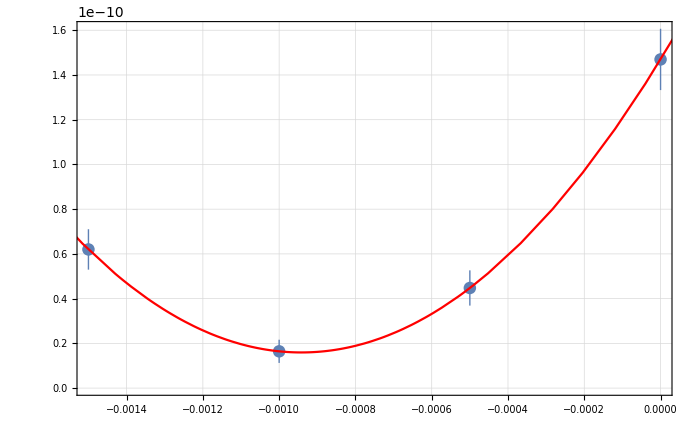
{b0 =  | -0.000941662
FittedModel[1.59389×10^-11+0.000147742 (0.000941662+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.000941662 | 0.0000353451 | -26.642 | 0.0238842
scale | 0.000147742 | 0.0000177887 | 8.30537 | 0.0762844
yoffset | 1.59389×10^-11 | 4.67397×10^-12 | 3.41013 | 0.181594 | 
 | DF | SS | MS
Model | 3 | 204.427 | 68.1423
Error | 1 | 2.39393×10^-7 | 2.39393×10^-7
Uncorrected Total | 4 | 204.427 | 
Corrected Total | 3 | 87.8348 |  | ,-Graphics-}

```mathematica
BRamp1000Fit=Chi2FitandPlot[BinInt35Bins1000[[All,2]]/Total[BinInt35Bins1000[[All,2]]],{BinInt35Bins1000bvary1/Total[BinInt35Bins1000bvary1[[All,2]]],BinInt35Bins1000bvary2/Total[BinInt35Bins1000bvary2[[All,2]]],BinInt35Bins1000bvary3/Total[BinInt35Bins1000bvary3[[All,2]]],BinInt35Bins1000bvary4/Total[BinInt35Bins1000bvary4[[All,2]]]},bvary,5]
```

```mathematica
BRamp1000Fit[[1,1,1,2]]/(5*10^-5)
```

-18.8332

## 0.6 T

```mathematica
BRxBList
```

{0.15,0.2,0.3,0.4,0.6,0.8,1.,1.2}

```mathematica
BinInt35Bins600=ParallelMap[
(BinInt[0.,#,{Pi,BRxBList[[5]],2.,1.,1.,1.,1.,1.,1.},{0.06,0.05,0.9,0.,-0.9,0.1,0.09,0.9,0.,-0.9},{0.01,0.035,0.,0.},
{IntOptionList[[6]],4,3,0,2},{IntOptionList[[6]],3,3,0,2},{IntOptionList[[6]],3,4}
]//AbsoluteTiming
)&,XY35BinsXOffBRamp[[5]],Method->"FinestGrained"]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {0.00343028,0.0176882}. NIntegrate obtained 0.0666911 and 0.000191246 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {0.00343028,-0.0163118}. NIntegrate obtained 0.071955 and 0.000286135 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {0.00800171,0.0176882}. NIntegrate obtained 0.187385 and 0.000572743 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {0.00800171,-0.0163118}. NIntegrate obtained 0.19665 and 0.000424103 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {0.0125731,-0.0163118}. NIntegrate obtained 0.247415 and 0.000386887 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {0.0125731,0.0176882}. NIntegrate obtained 0.244895 and 0.000363685 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {0.0171446,0.0176882}. NIntegrate obtained 0.169884 and 0.000301304 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {0.0171446,-0.0163118}. NIntegrate obtained 0.162269 and 0.000265185 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {0.021716,0.0176882}. NIntegrate obtained 0.0637937 and 0.000132505 for the integral and error estimates.

{{3388.88,0.00641307},{488.53,0.00914141},{485.593,0.00891845},{567.182,0.00870285},{3763.39,0.00585693},{7668.51,0.071955},{473.796,0.102912},{463.119,0.100815},{437.941,0.0987696},{7364.1,0.0666911},{10080.9,0.19665},{491.142,0.284687},{463.385,0.280894},{459.175,0.277121},{9415.87,0.187385},{10092.,0.247415},{499.036,0.36494},{601.997,0.363923},{574.659,0.362649},{11153.1,0.244895},{12232.,0.162269},{584.971,0.245543},{670.871,0.248771},{640.525,0.251602},{10832.6,0.169884},{2719.3,0.0565982},{862.512,0.0880581},{761.005,0.0912567},{832.359,0.0941224},{10210.6,0.0637937},{1412.4,0.0095471},{809.639,0.0153824},{804.709,0.0164035},{827.539,0.0173709},{1451.65,0.0119196}}

```mathematica
BinInt35Bins600={{3388.879175633483,0.006413068080874879},{488.529759991303,0.009141406952937081},{485.59310769881785,0.0089184450606778},{567.1821915364854,0.008702848611127368},{3763.389970845556,0.005856927590482322},{7668.513452171056,0.07195497995600833},{473.796385657348,0.10291243777984577},{463.1185891019867,0.10081509373003394},{437.9406712836425,0.09876961546309698},{7364.097035,0.0666911499555515},{10080.932458,0.19664981694813619},{491.141881,0.28468732537776786},{463.3850795844465,0.2808936193580458},{459.17507134626294,0.2771205497767808},{9415.871189198484,0.18738485333914856},{10091.966421343146,0.2474145819935553},{499.0362307108732,0.36494004746553255},{601.997112,0.3639230241291799},{574.6591473993261,0.36264945386980096},{11153.06998798919,0.24489545852321565},{12232.01356124358,0.1622690495736171},{584.9708642276927,0.24554283196122328},{670.871449,0.24877116667896362},{640.5253173368852,0.25160218141723634},{10832.641385018043,0.16988420745433325},{2719.302509,0.05659821009214654},{862.511736845212,0.08805808308962572},{761.0052662781119,0.09125666347331642},{832.3590398950751,0.09412239148923739},{10210.603771920369,0.06379374121785017},{1412.4027021755478,0.009547102829211562},{809.638939575835,0.01538238512538993},{804.709128,0.016403538765369503},{827.5388512032581,0.017370906183256582},{1451.6450363019026,0.01191959876217107}};
```

### took ~11000s, 3h

```mathematica
ListPlot3D[Transpose[{BinCentersBRamp[[5,All,1]],BinCentersBRamp[[5,All,2]],BinInt35Bins600[[All,2]]}]]
```

-Graphics3D-

```mathematica
BinInt35Bins600bvary1=ParallelMap[
(BinInt[-0.0015,#,{Pi,BRxBList[[5]]+BRxBList[[5]]*5*10^-5,2.,1.,1.,1.,1.,1.,1.},{0.06,0.05,0.9,0.,-0.9,0.1,0.09,0.9,0.,-0.9},{0.01,0.035,0.,0.},
{IntOptionList[[6]],4,3,0,2},{IntOptionList[[6]],3,3,0,2},{IntOptionList[[6]],3,4}
]//AbsoluteTiming
)&,XY35BinsXOffBRamp[[5]],Method->"FinestGrained"]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {0.00343028,0.0176882}. NIntegrate obtained 0.0666805 and 0.000191206 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {0.00343028,-0.0163118}. NIntegrate obtained 0.0719441 and 0.000286088 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {0.00800171,0.0176882}. NIntegrate obtained 0.187377 and 0.00057276 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {0.00800171,-0.0163118}. NIntegrate obtained 0.196643 and 0.00042408 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {0.0125731,-0.0163118}. NIntegrate obtained 0.247425 and 0.000386913 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {0.0125731,0.0176882}. NIntegrate obtained 0.244905 and 0.000363738 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {0.0171446,0.0176882}. NIntegrate obtained 0.169896 and 0.000301331 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {0.0171446,-0.0163118}. NIntegrate obtained 0.16228 and 0.000265207 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {0.021716,0.0176882}. NIntegrate obtained 0.0637948 and 0.000132507 for the integral and error estimates.

{{3439.55,0.00641117},{501.312,0.0091387},{496.047,0.00891579},{571.872,0.00870025},{3798.64,0.00585517},{7512.33,0.0719441},{479.756,0.102897},{467.1,0.100799},{446.005,0.098754},{7418.08,0.0666805},{10181.9,0.196643},{499.849,0.284677},{466.477,0.280883},{459.338,0.277109},{9158.52,0.187377},{10154.2,0.247425},{618.314,0.364955},{497.566,0.363938},{574.758,0.362664},{10804.6,0.244905},{11810.8,0.16228},{590.033,0.245559},{672.522,0.248788},{643.768,0.251619},{10905.8,0.169896},{2596.84,0.0565986},{912.474,0.0880587},{804.338,0.0912575},{842.071,0.0941236},{12004.7,0.0637948},{1418.86,0.00954557},{817.936,0.0153799},{756.577,0.016401},{832.203,0.0173683},{1463.2,0.0119179}}

```mathematica
BinInt35Bins600bvary1={{3439.5465212649437,0.006411174961905668},{501.31172666689264,0.00913869870216997},{496.04730299987494,0.008915790737490931},{571.8723341391868,0.008700247197040382},{3798.640178724955,0.005855170603899159},{7512.3298949824075,0.07194406791250185},{479.75588061306456,0.10289663653374848},{467.09980905892223,0.1007993790850762},{446.0045502490703,0.09875398691874447},{7418.080096,0.0666804591307565},{10181.90464,0.1966427747346593},{499.848576,0.2846769260451806},{466.47749256382025,0.28088287373168813},{459.33778926675035,0.27710946967836014},{9158.518164424906,0.1873769601825615},{10154.207518039811,0.2474247807865802},{618.313739,0.3649551087721053},{497.5658828665913,0.3639378020099679},{574.7577056530364,0.36266392154809707},{10804.591388018447,0.24490490954967317},{11810.817619190604,0.16227985309319135},{590.0328626753278,0.2455591656235257},{672.521793,0.24878783421397993},{643.7680473323427,0.2516192090943305},{10905.81743347801,0.16989585210942526},{2596.8364868124904,0.05659858457962043},{912.4742,0.08805871792357435},{804.338029,0.09125752372921032},{842.0712375316931,0.09412356117333012},{12004.695538,0.06379476259509624},{1418.8552129608956,0.00954556602263151},{817.9360885666225,0.015379929965075758},{756.5766516788186,0.01640098276829947},{832.2030850913359,0.01736829737146376},{1463.2024110160683,0.01191787359336961}};
```

```mathematica
BinInt35Bins600bvary2=ParallelMap[
(BinInt[-0.001,#,{Pi,BRxBList[[5]]+BRxBList[[5]]*5*10^-5,2.,1.,1.,1.,1.,1.,1.},{0.06,0.05,0.9,0.,-0.9,0.1,0.09,0.9,0.,-0.9},{0.01,0.035,0.,0.},
{IntOptionList[[6]],4,3,0,2},{IntOptionList[[6]],3,3,0,2},{IntOptionList[[6]],3,4}
]//AbsoluteTiming
)&,XY35BinsXOffBRamp[[5]],Method->"FinestGrained"]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {0.00343028,-0.0163118}. NIntegrate obtained 0.0719505 and 0.000286114 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {0.00343028,0.0176882}. NIntegrate obtained 0.0666867 and 0.000191227 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {0.00800171,0.0176882}. NIntegrate obtained 0.187385 and 0.000572779 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {0.00800171,-0.0163118}. NIntegrate obtained 0.19665 and 0.000424097 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {0.0125731,-0.0163118}. NIntegrate obtained 0.247422 and 0.000385817 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {0.0125731,0.0176882}. NIntegrate obtained 0.244904 and 0.000363743 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {0.0171446,0.0176882}. NIntegrate obtained 0.169888 and 0.000301318 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {0.0171446,-0.0163118}. NIntegrate obtained 0.162272 and 0.000265194 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {0.021716,0.0176882}. NIntegrate obtained 0.0637901 and 0.000132495 for the integral and error estimates.

{{3448.41,0.0064121},{501.373,0.00914002},{495.505,0.00891709},{574.454,0.00870152},{3803.48,0.00585603},{7393.84,0.0719505},{480.118,0.102906},{469.256,0.100809},{445.184,0.0987631},{7432.22,0.0666867},{10120.8,0.19665},{498.548,0.284688},{466.079,0.280894},{459.321,0.277121},{9168.58,0.187385},{10183.4,0.247422},{616.265,0.364953},{498.031,0.363936},{575.962,0.362662},{10893.9,0.244904},{11905.2,0.162272},{590.909,0.245548},{670.05,0.248777},{645.78,0.251608},{10916.1,0.169888},{2726.66,0.0565943},{868.129,0.0880521},{763.872,0.0912507},{970.255,0.0941166},{10163.9,0.0637901},{1417.46,0.00954467},{939.49,0.0153785},{805.833,0.0163995},{904.042,0.0173667},{1585.64,0.0119168}}

```mathematica
BinInt35Bins600bvary2={{3448.4067762829513,0.006412101217319912},{501.37314560784785,0.009140022739172315},{495.5049829391831,0.008917086775869968},{574.4544208377283,0.008701515987670534},{3803.4812703227776,0.005856026803581715},{7393.8428656303495,0.0719505246288405},{480.11845725255296,0.10290595073582083},{469.2560384474232,0.10080859940410418},{445.18399957397554,0.09876311401346974},{7432.221137,0.06668667792763694},{10120.780016,0.19665040132288525},{498.548328,0.28468808130586315},{466.0785614103976,0.2808941418020455},{459.32126253371626,0.2771208401261646},{9168.578206283091,0.18738485285411782},{10183.354718873506,0.2474221595117786},{616.264976,0.36495283525643296},{498.03081029236597,0.36393579940072474},{575.9620203054544,0.3626621968781095},{10893.942268233717,0.24490405421997963},{11905.151135060016,0.16227238586078516},{590.9088669490069,0.24554787200014486},{670.050387,0.24877653788497694},{645.7801495705108,0.2516079467971164},{10916.07716439754,0.16988841996843965},{2726.65504,0.056594331148226665},{868.1285952228801,0.08805211083256816},{763.8716938193091,0.0912507161844928},{970.2554199420504,0.09411658958910879},{10163.89203904525,0.06379008275596183},{1417.4589325906136,0.009544672095723843},{939.4896624911138,0.015378490569986815},{805.833398,0.01639945217835828},{904.0424247207102,0.017366682634085424},{1585.638727,0.011916771008603614}};
```

```mathematica
BinInt35Bins600bvary3=ParallelMap[
(BinInt[-0.0005,#,{Pi,BRxBList[[5]]+BRxBList[[5]]*5*10^-5,2.,1.,1.,1.,1.,1.,1.},{0.06,0.05,0.9,0.,-0.9,0.1,0.09,0.9,0.,-0.9},{0.01,0.035,0.,0.},
{IntOptionList[[6]],4,3,0,2},{IntOptionList[[6]],3,3,0,2},{IntOptionList[[6]],3,4}
]//AbsoluteTiming
)&,XY35BinsBRamp[[5]],Method->"FinestGrained"]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {0.00343028,0.0176882}. NIntegrate obtained 0.0666929 and 0.000191248 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {0.00343028,-0.0163118}. NIntegrate obtained 0.071957 and 0.000286141 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {0.00800171,0.0176882}. NIntegrate obtained 0.187393 and 0.000572765 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {0.00800171,-0.0163118}. NIntegrate obtained 0.196658 and 0.000424116 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {0.0125731,0.0176882}. NIntegrate obtained 0.244903 and 0.000363747 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {0.0125731,-0.0163118}. NIntegrate obtained 0.247421 and 0.000385817 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {0.0171446,0.0176882}. NIntegrate obtained 0.169881 and 0.000301305 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {0.0171446,-0.0163118}. NIntegrate obtained 0.162265 and 0.000265184 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {0.021716,0.0176882}. NIntegrate obtained 0.0637854 and 0.000132484 for the integral and error estimates.

{{3764.19,0.00641303},{548.488,0.00914135},{546.262,0.00891838},{536.879,0.00870278},{3679.62,0.00585688},{7904.37,0.071957},{482.804,0.102915},{480.716,0.100818},{463.865,0.0987722},{7533.75,0.0666929},{10300.,0.196658},{495.445,0.284699},{491.434,0.280905},{478.115,0.277132},{9485.73,0.187393},{12434.7,0.247421},{552.44,0.364951},{544.614,0.363934},{549.026,0.36266},{11765.4,0.244903},{12674.2,0.162265},{639.54,0.245537},{597.732,0.248765},{605.63,0.251597},{11388.2,0.169881},{2494.24,0.0565901},{814.45,0.0880455},{719.283,0.0912439},{919.032,0.0941096},{10024.6,0.0637854},{1414.96,0.00954378},{884.771,0.0153771},{737.358,0.0163979},{871.25,0.0173651},{1421.49,0.0119157}}

```mathematica
BinInt35Bins600bvary4=ParallelMap[
(BinInt[-0.00,#,{Pi,BRxBList[[5]]+BRxBList[[5]]*5*10^-5,2.,1.,1.,1.,1.,1.,1.},{0.06,0.05,0.9,0.,-0.9,0.1,0.09,0.9,0.,-0.9},{0.01,0.035,0.,0.},
{IntOptionList[[6]],4,3,0,2},{IntOptionList[[6]],3,3,0,2},{IntOptionList[[6]],3,4}
]//AbsoluteTiming
)&,XY35BinsBRamp[[5]],Method->"FinestGrained"]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {0.00343028,0.0176882}. NIntegrate obtained 0.0666991 and 0.000191269 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {0.00343028,-0.0163118}. NIntegrate obtained 0.0719634 and 0.000286169 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {0.00800171,-0.0163118}. NIntegrate obtained 0.196666 and 0.000424136 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {0.00800171,0.0176882}. NIntegrate obtained 0.187401 and 0.000572783 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {0.0125731,0.0176882}. NIntegrate obtained 0.244902 and 0.000363751 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {0.0125731,-0.0163118}. NIntegrate obtained 0.247419 and 0.000385817 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {0.0171446,0.0176882}. NIntegrate obtained 0.169874 and 0.00030129 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {0.0171446,-0.0163118}. NIntegrate obtained 0.162257 and 0.000265171 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {0.021716,0.0176882}. NIntegrate obtained 0.0637822 and 0.000132672 for the integral and error estimates.

{{3339.05,0.00641395},{560.454,0.00914267},{586.406,0.00891968},{583.099,0.00870405},{3952.55,0.00585774},{7319.44,0.0719634},{448.82,0.102925},{480.043,0.100827},{473.577,0.0987814},{7294.26,0.0666991},{9107.67,0.196666},{489.516,0.28471},{496.743,0.280917},{410.423,0.277144},{9709.24,0.187401},{11554.,0.247419},{606.077,0.364948},{465.931,0.363932},{593.339,0.362659},{10112.7,0.244902},{13588.,0.162257},{697.697,0.245525},{656.857,0.248754},{661.652,0.251585},{10229.8,0.169874},{2678.07,0.0565858},{873.589,0.0880389},{767.86,0.0912371},{984.608,0.0941027},{9836.3,0.0637822},{1486.01,0.00954289},{968.534,0.0153756},{718.636,0.0163964},{908.919,0.0173635},{1490.88,0.0119146}}

```mathematica
bvary=-{0.0015,0.001,0.0005,0.}
```

{-0.0015,-0.001,-0.0005,0.}

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

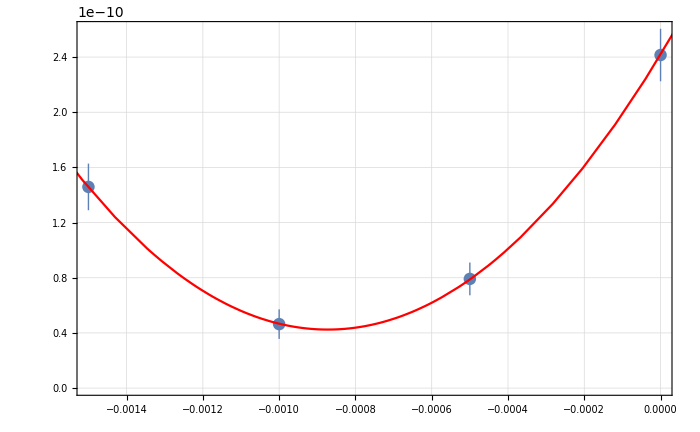
{b0 =  | -0.000872424
FittedModel[4.24337×10^-11+0.00026194 (0.000872424+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.000872424 | 0.0000310591 | -28.0891 | 0.0226547
scale | 0.00026194 | 0.0000299332 | 8.75082 | 0.0724355
yoffset | 4.24337×10^-11 | 8.92863×10^-12 | 4.75255 | 0.132027 | 
 | DF | SS | MS
Model | 3 | 298.455 | 99.4848
Error | 1 | 0.00249867 | 0.00249867
Uncorrected Total | 4 | 298.457 | 
Corrected Total | 3 | 90.5287 |  | ,-Graphics-}

```mathematica
BRamp600Fit=Chi2FitandPlot[BinInt35Bins600[[All,2]]/Total[BinInt35Bins600[[All,2]]],{BinInt35Bins600bvary1/Total[BinInt35Bins600bvary1[[All,2]]],BinInt35Bins600bvary2/Total[BinInt35Bins600bvary2[[All,2]]],BinInt35Bins600bvary3/Total[BinInt35Bins600bvary3[[All,2]]],BinInt35Bins600bvary4/Total[BinInt35Bins600bvary4[[All,2]]]},bvary,5]
```

```mathematica
BRamp600Fit[[1,1,1,2]]/(5*10^-5)
```

-17.4485

# rF Sensitivity

## 0.2 T

```mathematica
CloseKernels[]
LaunchKernels[]
```

{KernelObject[1,192.168.0.220,<defunct>],KernelObject[2,192.168.0.220,<defunct>],KernelObject[3,192.168.0.220,<defunct>],KernelObject[4,192.168.0.220,<defunct>],KernelObject[5,192.168.0.220,<defunct>],KernelObject[6,192.168.0.220,<defunct>],KernelObject[7,192.168.0.150,<defunct>],KernelObject[8,192.168.0.150,<defunct>],KernelObject[9,local,<defunct>],KernelObject[10,local,<defunct>],KernelObject[11,local,<defunct>]}

{KernelObject[12,192.168.0.220],KernelObject[13,192.168.0.220],KernelObject[14,192.168.0.220],KernelObject[15,192.168.0.220],KernelObject[16,192.168.0.220],KernelObject[17,192.168.0.220],KernelObject[18,192.168.0.150],KernelObject[19,192.168.0.150],KernelObject[20,192.168.0.150],KernelObject[21,local],KernelObject[22,local],KernelObject[23,local]}

```mathematica
BinInt35BinsrFData=ParallelMap[
(BinInt[0.,#,{Pi,0.2,2.,1.,1.,1.,1.,1.,1.},{0.06,0.05,0.9,0.,-0.9,0.1,0.09,0.9,0.,-0.9},{0.01,0.035,-0.03,0.},
{IntOptionList[[6]],3,3,0,2},{IntOptionList[[6]],3,3,0,2},{IntOptionList[[6]],3,4}
]//AbsoluteTiming
)&,XY35BinsBRamp[[2]],Method->"FinestGrained"]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {0.00464713,-0.0163118}. NIntegrate obtained 0.21763 and 0.000253173 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {0.0160757,-0.0183118}. NIntegrate obtained 0.15826 and 0.000217255 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {0.0160757,0.0196882}. NIntegrate obtained 0.164137 and 0.000271451 for the integral and error estimates.

{{8405.07,0.21763},{1083.77,0.33608},{428.614,0.352978},{1162.61,0.333146},{14809.4,0.213776},{10006.9,0.15826},{1715.62,0.243207},{1302.85,0.266606},{1735.18,0.248471},{19641.4,0.164137},{2151.48,0.0657993},{1973.71,0.101641},{2187.54,0.115035},{2131.63,0.108228},{2272.15,0.0738086},{1548.55,0.0146454},{1639.8,0.0228983},{2018.96,0.0269409},{2353.38,0.0253556},{1956.03,0.0177598},{1971.01,0.00192512},{1709.29,0.00309764},{2122.12,0.00376203},{1583.44,0.00357303},{1902.6,0.0025364},{1341.73,0.0000769138},{1793.33,0.00013286},{1414.83,0.000217959},{1615.61,0.000178699},{1590.96,0.000132334},{18.7624,1.55597×10^-7},{66.7706,1.70707×10^-7},{117.879,1.56434×10^-7},{135.892,4.4142×10^-7},{156.079,2.82839×10^-7}}

```mathematica
BinInt35BinsrFData={{8405.072324707622,0.21763027914973174},{1083.7679270317644,0.33608049116763256},{428.6135181920138,0.3529783305952771},{1162.6072269529757,0.33314609349755886},{14809.436370618172,0.21377585818249187},{10006.948053247923,0.1582597096909707},{1715.6152257283206,0.24320664483650895},{1302.851506730659,0.26660637294196077},{1735.1769875556674,0.24847092951495955},{19641.35321,0.16413702826497742},{2151.479696,0.06579931948121294},{1973.713497,0.1016412427273571},{2187.5414113086395,0.11503467742663515},{2131.6301498271523,0.10822798593522544},{2272.1485516451985,0.07380856945268002},{1548.5455154901738,0.014645428780536613},{1639.8044740915736,0.022898305158944858},{2018.9648535205365,0.026940885680857965},{2353.379174,0.025355579886088803},{1956.03142,0.017759838344107638},{1971.0133607426171,0.001925118642861074},{1709.2931421596147,0.003097637250962248},{2122.1201122677076,0.0037620315620654787},{1583.4413747534616,0.0035730343994022193},{1902.5968653839739,0.002536399605758308},{1341.7313882226695,0.00007691383005837895},{1793.334532,0.00013286047608077498},{1414.832071,0.00021795920938589707},{1615.612936927343,0.00017869919648643532},{1590.9609879660925,0.00013233445644380906},{18.76242614072561,1.5559735940600962*^-7},{66.77056202162613,1.707072995450891*^-7},{117.87867572173066,1.5643410858806957*^-7},{135.89197075641775,4.414201472170746*^-7},{156.07900396244287,2.828388763168843*^-7}};
```

```mathematica
BinInt35BinsrFVary1=ParallelMap[
(BinInt[-0.0015,#,{Pi,0.2,2.+2*10^-4,1.,1.,1.,1.,1.,1.},{0.06,0.05,0.9,0.,-0.9,0.1,0.09,0.9,0.,-0.9},{0.01,0.035,-0.03,0.},
{IntOptionList[[6]],3,3,0,2},{IntOptionList[[6]],3,3,0,2},{IntOptionList[[6]],3,4}
]//AbsoluteTiming
)&,XY35BinsBRamp[[2]],Method->"FinestGrained"]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {0.00464713,-0.0163118}. NIntegrate obtained 0.217603 and 0.000259306 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {0.0160757,-0.0183118}. NIntegrate obtained 0.158265 and 0.000217156 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {0.0160757,0.0196882}. NIntegrate obtained 0.164143 and 0.000273321 for the integral and error estimates.

{{7572.77,0.217603},{890.33,0.336047},{360.834,0.352941},{1112.31,0.333111},{15009.2,0.213752},{10429.9,0.158265},{2024.74,0.243215},{1534.94,0.266615},{1903.74,0.248479},{19544.2,0.164143},{2210.96,0.0658056},{2118.47,0.101651},{1839.63,0.115046},{1757.58,0.108239},{2169.6,0.0738156},{1831.32,0.0146464},{1801.9,0.0229003},{2383.1,0.026943},{2345.73,0.0253577},{1517.58,0.0177612},{2126.69,0.00192502},{1594.72,0.00309752},{2030.77,0.00376191},{1885.62,0.00357286},{1805.45,0.00253632},{1242.22,0.0000768819},{1382.9,0.000132809},{1532.84,0.000216712},{1697.57,0.000178639},{1938.87,0.000132291},{17.771,1.55167×10^-7},{62.9025,1.70299×10^-7},{111.26,1.56057×10^-7},{128.46,4.40503×10^-7},{177.634,2.82209×10^-7}}

```mathematica
BinInt35BinsrFVary1={{7572.767895446825,0.2176030688953423},{890.3295885064216,0.33604727720153454},{360.83425261464765,0.35294079139485224},{1112.3086017800636,0.3331112832359524},{15009.202807205973,0.21375226358211366},{10429.885077338835,0.15826533477993238},{2024.7353255750688,0.24321547357487014},{1534.9394185536214,0.2666145845858478},{1903.7371429158038,0.2484789517005884},{19544.211026,0.1641431553657814},{2210.95534,0.06580563072673186},{2118.47108,0.1016513872498168},{1839.6312046374562,0.11504605197028078},{1757.5760687996876,0.10823875770295545},{2169.6022843636197,0.07381558984416461},{1831.3243216972198,0.014646385996793704},{1801.8995676236818,0.022900269486670073},{2383.1034312291317,0.0269429848705108},{2345.725614,0.02535773557702395},{1517.583639792909,0.017761205639729744},{2126.692251,0.0019250172437845301},{1594.7187536894967,0.0030975204562697857},{2030.7737794142934,0.0037619086335200775},{1885.6168436207972,0.0035728622107844784},{1805.452991025256,0.0025363231518457617},{1242.2158707679648,0.00007688190434860095},{1382.8950049621903,0.00013280918953165573},{1532.836009,0.0002167120335437029},{1697.5684815051495,0.0001786388228340583},{1938.865434,0.00013229054881873625},{17.770958678806597,1.5516650290850567*^-7},{62.902536795605684,1.7029911741785653*^-7},{111.26013040799842,1.5605671910005457*^-7},{128.4597089432814,4.405025388908246*^-7},{177.6335541731148,2.82208820875456*^-7}};
```

```mathematica
Print[DateString[]]
BinInt35BinsrFVary2=ParallelMap[
(BinInt[-0.001,#,{Pi,0.2,2.+2*10^-4,1.,1.,1.,1.,1.,1.},{0.06,0.05,0.9,0.,-0.9,0.1,0.09,0.9,0.,-0.9},{0.01,0.035,-0.03,0.},
{IntOptionList[[6]],3,3,0,2},{IntOptionList[[6]],3,3,0,2},{IntOptionList[[6]],3,4}
]//AbsoluteTiming
)&,XY35BinsBRamp[[2]],Method->"FinestGrained"]
```

Sat 4 Apr 2020 00:13:35

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {0.00464713,-0.0163118}. NIntegrate obtained 0.217602 and 0.000259292 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {0.0160757,-0.0183118}. NIntegrate obtained 0.158258 and 0.000217139 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {0.0160757,0.0196882}. NIntegrate obtained 0.164136 and 0.000273301 for the integral and error estimates.

{{7496.38,0.217602},{891.458,0.336047},{362.404,0.35294},{1216.33,0.333111},{14843.1,0.213753},{10085.2,0.158258},{1909.36,0.243204},{1551.48,0.266602},{1911.2,0.248468},{19130.1,0.164136},{2080.67,0.0658005},{1590.29,0.101644},{1835.63,0.115037},{2216.45,0.108231},{2361.74,0.07381},{1714.71,0.014645},{1799.84,0.0228981},{1932.69,0.0269405},{2300.71,0.0253554},{1522.51,0.0177596},{2070.38,0.00192481},{1876.2,0.00309719},{2025.57,0.00376151},{1512.49,0.00357249},{1978.3,0.00253606},{1250.8,0.0000768729},{1754.52,0.000132794},{1169.19,0.000216687},{1564.52,0.000178618},{1458.91,0.000132275},{21.9053,1.55147×10^-7},{78.7681,1.70278×10^-7},{139.672,1.56037×10^-7},{148.042,4.40447×10^-7},{180.244,2.82173×10^-7}}

```mathematica
BinInt35BinsrFVary2={{7496.376126428894,0.21760241442118655},{891.4580332542733,0.33604663228876197},{362.4037916628189,0.3529401830746159},{1216.3347057223295,0.33311138316186917},{14843.105461902893,0.21375250449213307},{10085.215695087118,0.15825769006729695},{1909.3646708319538,0.2432040288833689},{1551.4845415361006,0.2666021025951495},{1911.2011749677274,0.2484676916518787},{19130.053891,0.16413577094648102},{2080.665016,0.06580053422514409},{1590.2889301073446,0.10164361630886415},{1835.6254215523882,0.11503732937136653},{2216.4454226752796,0.10823059671703578},{2361.7398273831063,0.07381002191701291},{1714.7079637699571,0.014645018113551367},{1799.841075236944,0.022898146422772516},{1932.6856087128815,0.026940496654460355},{2300.70906,0.02535539959180737},{1522.513456069127,0.01775956572056401},{2070.375427307654,0.001924812993092289},{1876.1994529050505,0.003097193793356271},{2025.5749527138528,0.0037615128368344544},{1512.485820643413,0.0035724883756958615},{1978.30253831012,0.002536057695560572},{1250.8018557656678,0.00007687287653371136},{1754.524355,0.00013279365941260864},{1169.187715744229,0.00021668703883607712},{1564.5195627988267,0.00017861807817092925},{1458.905998639343,0.00013227520307451673},{21.905272437501445,1.5514686377888982*^-7},{78.768068826046,1.7027758356302466*^-7},{139.67169811804985,1.5603702519374618*^-7},{148.04225212948063,4.4044715497857627*^-7},{180.2444491709205,2.821732857009479*^-7}};
```

### took 16039s, 4.5h

```mathematica
Print[DateString[]]
BinInt35BinsrFVary3=ParallelMap[
(BinInt[-0.0005,#,{Pi,0.2,2.+2*10^-4,1.,1.,1.,1.,1.,1.},{0.06,0.05,0.9,0.,-0.9,0.1,0.09,0.9,0.,-0.9},{0.01,0.035,-0.03,0.},
{IntOptionList[[6]],3,3,0,2},{IntOptionList[[6]],3,3,0,2},{IntOptionList[[6]],3,4}
]//AbsoluteTiming
)&,XY35BinsBRamp[[2]],Method->"FinestGrained"]
```

Sat 4 Apr 2020 05:32:26

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {0.00464713,-0.0163118}. NIntegrate obtained 0.217602 and 0.000259279 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {0.0160757,-0.0183118}. NIntegrate obtained 0.15825 and 0.000217122 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {0.0160757,0.0196882}. NIntegrate obtained 0.164128 and 0.000273281 for the integral and error estimates.

{{7506.33,0.217602},{898.932,0.336046},{365.046,0.35294},{1219.38,0.333111},{14976.6,0.213753},{10176.,0.15825},{1920.86,0.243193},{1554.73,0.26659},{1917.63,0.248456},{19148.7,0.164128},{2092.85,0.0657954},{1586.25,0.101636},{1836.48,0.115029},{2215.97,0.108222},{2361.54,0.0738045},{1699.5,0.0146437},{1818.77,0.022896},{1930.89,0.026938},{2306.03,0.0253531},{1526.97,0.0177579},{2077.16,0.00192461},{1862.04,0.00309687},{2051.51,0.00376112},{1513.69,0.00357211},{1983.82,0.00253579},{1251.77,0.0000768639},{1751.18,0.000132778},{1169.78,0.000216662},{1650.55,0.000178597},{1610.67,0.00013226},{17.8577,1.55127×10^-7},{63.3124,1.70256×10^-7},{111.911,1.56017×10^-7},{129.54,4.40392×10^-7},{171.298,2.82138×10^-7}}

```mathematica
BinInt35BinsrFVary3={{7506.334105619257,0.2176017603762766},{898.9320629970227,0.33604598779896433},{365.0458654843133,0.3529395751533547},{1219.3750368921774,0.3331114830222482},{14976.644173666557,0.2137527843236471},{10176.029085150994,0.1582500503685494},{1920.8638595248544,0.24319259169802265},{1554.730078865851,0.2665896811634985},{1917.6309511894037,0.24845643898822392},{19148.747585,0.16412838544571434},{2092.846135,0.06579544106616558},{1586.2541827932982,0.10163584453720563},{1836.4826133384145,0.11502861249328629},{2215.972196451165,0.10822244108360869},{2361.5430602285646,0.07380445764166124},{1699.497687662486,0.01464365112745369},{1818.768305577584,0.02289602475131501},{1930.886796307055,0.02693801007033992},{2306.032875,0.025353065138678167},{1526.9656697086627,0.017757926876961337},{2077.1615245387516,0.001924608876360616},{1862.0433556867847,0.003096867344689026},{2051.5071888417524,0.003761117299737419},{1513.6864974066857,0.003572114785792022},{1983.8226159954215,0.002535792413378463},{1251.7732851804099,0.00007686385335045887},{1751.184688,0.00013277814189897638},{1169.784963569691,0.00021666205670531252},{1650.5545786079267,0.0001785973471134669},{1610.6684095814437,0.00013225986739501022},{17.857746744768075,1.551272375298616*^-7},{63.312388292270086,1.702560638314615*^-7},{111.91141379757771,1.5601734420395152*^-7},{129.5395645546478,4.403918073906125*^-7},{171.29805575017517,2.8213777383266275*^-7}};
```

```mathematica
Print[DateString[]]
BinInt35BinsrFVary4=ParallelMap[
(BinInt[0.0,#,{Pi,0.2,2.+2*10^-4,1.,1.,1.,1.,1.,1.},{0.06,0.05,0.9,0.,-0.9,0.1,0.09,0.9,0.,-0.9},{0.01,0.035,-0.03,0.},
{IntOptionList[[6]],3,3,0,2},{IntOptionList[[6]],3,3,0,2},{IntOptionList[[6]],3,4}
]//AbsoluteTiming
)&,XY35BinsBRamp[[2]],Method->"FinestGrained"]
```

Sun 5 Apr 2020 00:49:53

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {0.00464713,-0.0163118}. NIntegrate obtained 0.217601 and 0.000259265 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {0.0160757,-0.0183118}. NIntegrate obtained 0.158242 and 0.000217106 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {0.0160757,0.0196882}. NIntegrate obtained 0.164121 and 0.000273255 for the integral and error estimates.

{{9117.6,0.217601},{1101.78,0.336045},{447.658,0.352939},{1221.73,0.333112},{15037.9,0.213753},{10239.9,0.158242},{1923.4,0.243181},{1558.82,0.266577},{1915.33,0.248445},{19205.,0.164121},{2110.21,0.0657904},{1947.06,0.101628},{2256.64,0.11502},{2219.87,0.108214},{2363.98,0.0737989},{1697.66,0.0146423},{1823.56,0.0228939},{2445.16,0.0269355},{2244.49,0.0253507},{1873.,0.0177563},{2071.32,0.0019244},{1862.28,0.00309654},{2049.11,0.00376072},{1897.98,0.00357174},{1999.5,0.00253553},{1546.4,0.0000768548},{1692.8,0.000132763},{1335.98,0.000216637},{1756.32,0.000178577},{1619.76,0.000132245},{21.738,1.55108×10^-7},{79.0092,1.70235×10^-7},{139.283,1.55998×10^-7},{162.487,4.40336×10^-7},{182.788,2.82102×10^-7}}

```mathematica
BinInt35BinsrFVary4={{9117.596306821171,0.21760110676019007},{1101.783812738977,0.33604534373172545},{447.6580098168373,0.35293896763067595},{1221.7300227255812,0.33311158408639796},{15037.861491047071,0.21375303830217623},{10239.886059312355,0.15824241567875838},{1923.4029812728893,0.24318116201144938},{1558.8176265690404,0.2665772678759398},{1915.3270039189117,0.24844519370236057},{19204.968155,0.16412100567539434},{2110.214646,0.06579035124650887},{1947.063112456442,0.10162807786109719},{2256.637754261113,0.11501990133041363},{2219.8685092224027,0.10821428951763995},{2363.97635243514,0.07379889701451808},{1697.6579084637713,0.014642285003827454},{1823.5556337241978,0.022893904470928112},{2445.164186,0.02693552511654452},{2244.4888894279043,0.025350732216129556},{1873.0016882552145,0.017756289078741563},{2071.323650901196,0.0019244048934577616},{1862.2781278791938,0.0030965411100573473},{2049.114298381364,0.003760721906285831},{1897.980466073312,0.003571741440831825},{1999.497323,0.002535527324071983},{1546.3967423132808,0.00007685483737193241},{1692.7960899226039,0.00013276263214087141},{1335.9823511031723,0.00021663709476828295},{1756.3201400491212,0.00017857662964829035},{1619.7583947347484,0.00013224454177031828},{21.737987907065076,1.5510762414875315*^-7},{79.00919128497699,1.7023455820927715*^-7},{139.28297134087344,1.5599767611796742*^-7},{162.48657285146376,4.4033649609120933*^-7},{182.7877649570002,2.82102285247679*^-7}};
```

```mathematica
Print[DateString[]]
BinInt35BinsrFVary5=ParallelMap[
(BinInt[0.0005,#,{Pi,0.2,2.+2*10^-4,1.,1.,1.,1.,1.,1.},{0.06,0.05,0.9,0.,-0.9,0.1,0.09,0.9,0.,-0.9},{0.01,0.035,-0.03,0.},
{IntOptionList[[6]],3,3,0,2},{IntOptionList[[6]],3,3,0,2},{IntOptionList[[6]],3,4}
]//AbsoluteTiming
)&,XY35BinsBRamp[[2]],Method->"FinestGrained"]
```

Sun 5 Apr 2020 06:09:58

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {0.00464713,-0.0163118}. NIntegrate obtained 0.2176 and 0.000259253 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {0.0160757,-0.0183118}. NIntegrate obtained 0.158235 and 0.000216817 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {0.0160757,0.0196882}. NIntegrate obtained 0.164114 and 0.000273235 for the integral and error estimates.

{{9124.54,0.2176},{1102.58,0.336045},{445.984,0.352938},{1218.9,0.333112},{15064.2,0.213753},{10269.6,0.158235},{1926.23,0.24317},{1555.41,0.266565},{1914.55,0.248434},{19187.2,0.164114},{2099.89,0.0657853},{1937.81,0.10162},{2258.28,0.115011},{2221.96,0.108206},{2373.79,0.0737933},{1705.54,0.0146409},{1829.89,0.0228918},{2434.43,0.026933},{2232.33,0.0253484},{1866.72,0.0177547},{2075.78,0.0019242},{1864.92,0.00309622},{2055.9,0.00376033},{1903.47,0.00357137},{1992.3,0.00253526},{1518.98,0.0000768458},{1692.32,0.000132747},{1340.4,0.000216612},{1766.48,0.000178556},{1628.2,0.000132229},{21.8711,1.55088×10^-7},{77.7573,1.70213×10^-7},{140.789,1.55978×10^-7},{162.669,4.40281×10^-7},{182.137,2.82067×10^-7}}

```mathematica
BinInt35BinsrFVary5={{9124.541554691052,0.21760045302033826},{1102.58490927199,0.33604470008662984},{445.9837308540695,0.35293836050618804},{1218.8987380308945,0.333111683815904},{15064.22550776468,0.2137532782223916},{10269.635101398952,0.15823487753801363},{1926.2287465770476,0.24316980489768697},{1555.4088830588555,0.2665648627244668},{1914.5456625706727,0.24843395578703528},{19187.183304,0.16411362986262407},{2099.88995,0.06578526476289093},{1937.8141697712015,0.10162031627552916},{2258.2820040819715,0.11501119587712978},{2221.9638989192836,0.10820614457345587},{2373.7857892616175,0.07379334003199677},{1705.5364331103121,0.014640919809376363},{1829.8925154433862,0.02289178558024421},{2434.425637,0.026933041791471306},{2232.328618570632,0.02534840082265675},{1866.7186680639509,0.017754652383096727},{2075.783513174678,0.0019242010442521538},{1864.9150777366297,0.003096215089250803},{2055.898544266763,0.003760326887612058},{1903.4730266855554,0.003571368340574457},{1992.297869,0.002535262389580198},{1518.9843994931434,0.00007684582778171759},{1692.323996252348,0.0001327471374710009},{1340.4020894446028,0.0002166121491921454},{1766.4819414396034,0.00017855592576203634},{1628.1979775387592,0.00013222922619055564},{21.871076597142558,1.5508802362291356*^-7},{77.75733416485093,1.7021306668259992*^-7},{140.78874127740607,1.559780209231075*^-7},{162.66901108433487,4.402812210446899*^-7},{182.13733694616639,2.8206681992310597*^-7}};
```

```mathematica
bList={-0.0015,-0.001,-0.0005,0.,0.0005};
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

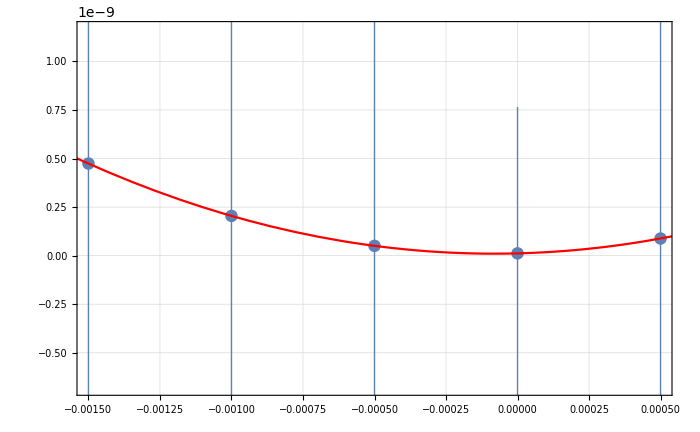
{b0 =  | -0.0000819722
FittedModel[1.03202×10^-11+0.000230603 (0.0000819722+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.0000819722 | 0.00552399 | -0.0148393 | 0.989508
scale | 0.000230603 | 0.00299456 | 0.0770074 | 0.945628
yoffset | 1.03202×10^-11 | 7.17604×10^-10 | 0.0143814 | 0.989831 | 
 | DF | SS | MS
Model | 3 | 0.0131518 | 0.00438393
Error | 2 | 1.23666×10^-8 | 6.18329×10^-9
Uncorrected Total | 5 | 0.0131518 | 
Corrected Total | 4 | 0.0101108 |  | ,-Graphics-}

```mathematica
rFfit=Chi2FitandPlot[BinInt35BinsrFData[[All,2]]/Total[BinInt35BinsrFData[[All,2]]],{BinInt35BinsrFVary1/Total[BinInt35BinsrFVary1[[All,2]]],BinInt35BinsrFVary2/Total[BinInt35BinsrFVary2[[All,2]]],BinInt35BinsrFVary3/Total[BinInt35BinsrFVary3[[All,2]]],BinInt35BinsrFVary4/Total[BinInt35BinsrFVary4[[All,2]]],BinInt35BinsrFVary5/Total[BinInt35BinsrFVary5[[All,2]]]},bList,3]
```

```mathematica
rFfit[[1,1,1,2]]/(10^-4)
```

-0.819722

# nbeam plateau k Sensitivity (k2x)

## 0.2 T

## Data

```mathematica
CloseKernels[]
LaunchKernels[]
```

{}

{KernelObject[1,192.168.0.220],KernelObject[2,192.168.0.220],KernelObject[3,192.168.0.220],KernelObject[4,192.168.0.220],KernelObject[5,192.168.0.220],KernelObject[6,192.168.0.220],KernelObject[7,192.168.0.150],KernelObject[8,192.168.0.150],KernelObject[9,192.168.0.150],KernelObject[10,local],KernelObject[11,local],KernelObject[12,local]}

```mathematica
Print[DateString[]]
t0=AbsoluteTime[];
BinInt35Binsk2xDataXOff=ParallelMap[
(BinInt[0.,#,{Pi,BRxBList[[2]],2.,1.,1.,1.,1.,1.,1.},{0.06,0.05,0.9,0.,-0.9,0.1,0.09,0.9,0.,-0.9},{0.01,0.035,XOffBRamp[[2]],0.},
{IntOptionList[[6]],3,3,0,2},{IntOptionList[[6]],3,3,0,2},{IntOptionList[[6]],3,4}
]//AbsoluteTiming
)&,XY35BinsBRampXOff[[2]],Method->"FinestGrained"]
t1=AbsoluteTime[];
(t1-t0)/3600.
```

Tue 14 Apr 2020 12:15:49

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {-0.0239243,-0.0163118}. NIntegrate obtained 0.0960178 and 0.00011818 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {-0.0124957,0.0196882}. NIntegrate obtained 0.192103 and 0.000428453 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {-0.0239243,0.0176882}. NIntegrate obtained 0.0891125 and 0.000201447 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {-0.0124957,-0.0163118}. NIntegrate obtained 0.200842 and 0.000247382 for the integral and error estimates.

{{629.49,0.00966887},{164.592,0.0137704},{161.095,0.0134301},{167.802,0.0131012},{593.617,0.00882806},{7406.87,0.0960178},{244.277,0.142887},{217.839,0.140269},{314.945,0.136928},{8349.84,0.0891125},{9345.85,0.200842},{3192.97,0.309538},{223.989,0.314215},{637.062,0.301836},{8078.57,0.192103},{2216.38,0.205755},{1422.06,0.316533},{633.264,0.338879},{1517.64,0.317214},{15434.2,0.205675},{10271.6,0.122281},{2047.16,0.187971},{4651.07,0.20843},{2133.97,0.194647},{9629.94,0.13016},{1602.62,0.0400127},{2063.55,0.0622493},{2573.39,0.0714921},{2142.6,0.0674373},{1935.23,0.0465161},{1703.98,0.00734895},{1756.42,0.0115482},{2757.64,0.0137466},{1766.74,0.0129054},{1652.73,0.00909479}}

4.45222

```mathematica
ListPlot3D[Transpose[{BinCentersBRampXOff[[2,All,1]],BinCentersBRampXOff[[2,All,2]],BinInt35Binsk2xDataXOff[[All,2]]}]]
```

-Graphics3D-

```mathematica
ListPlot3D[Transpose[{BinCentersBRampXOff[[2,All,1]],BinCentersBRampXOff[[2,All,2]],BinInt35Binsk2xDataXOff[[All,1]]}],PlotRange->All]
```

-Graphics3D-

## b variation

```mathematica
Print[DateString[]]
t0=AbsoluteTime[];
BinInt35Binsk2xVary1XOff=ParallelMap[
(BinInt[0.,#,{Pi,BRxBList[[2]],2.,1.,1.,1.,1.,1.,1.},{0.06,0.05,0.9,0.001,-0.9,0.1,0.09,0.9,0.,-0.9},{0.01,0.035,XOffBRamp[[2]],0.},
{IntOptionList[[6]],3,3,0,2},{IntOptionList[[6]],3,3,0,2},{IntOptionList[[6]],3,4}
]//AbsoluteTiming
)&,XY35BinsBRampXOff[[2]],Method->"FinestGrained"]
t1=AbsoluteTime[];
(t1-t0)/3600.
```

Tue 14 Apr 2020 17:43:04

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {-0.0239243,-0.0163118}. NIntegrate obtained 0.0959863 and 0.000129676 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {-0.0239243,0.0176882}. NIntegrate obtained 0.0890769 and 0.000200749 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {-0.0124957,-0.0163118}. NIntegrate obtained 0.200795 and 0.000240345 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {-0.0124957,0.0196882}. NIntegrate obtained 0.192057 and 0.000427881 for the integral and error estimates.

{{589.076,0.00966245},{165.173,0.0137612},{164.564,0.0134211},{160.962,0.0130925},{569.1,0.00882225},{7170.82,0.0959863},{283.784,0.142832},{252.27,0.140215},{368.098,0.136876},{7371.32,0.0890769},{8645.98,0.200795},{2853.15,0.309462},{255.504,0.314133},{711.17,0.301762},{9078.74,0.192057},{2567.43,0.205748},{1451.57,0.316525},{636.735,0.338861},{1706.72,0.317201},{15465.4,0.205666},{10193.5,0.122326},{2264.34,0.188039},{5021.03,0.208501},{2484.46,0.194712},{11741.7,0.130201},{1827.03,0.0400522},{2051.7,0.0623098},{2629.47,0.0715606},{2229.92,0.0674989},{2091.97,0.0465574},{1698.89,0.00736229},{3252.33,0.0115694},{2787.49,0.0137708},{1713.25,0.012928},{1908.89,0.00910975}}

4.64105

```mathematica
Print[DateString[]]
t0=AbsoluteTime[];
BinInt35Binsk2xVary2XOff=ParallelMap[
(BinInt[0.001,#,{Pi,BRxBList[[2]],2.,1.,1.,1.,1.,1.,1.},{0.06,0.05,0.9,0.001,-0.9,0.1,0.09,0.9,0.,-0.9},{0.01,0.035,XOffBRamp[[2]],0.},
{IntOptionList[[6]],3,3,0,2},{IntOptionList[[6]],3,3,0,2},{IntOptionList[[6]],3,4}
]//AbsoluteTiming
)&,XY35BinsBRampXOff[[2]],Method->"FinestGrained"]
t1=AbsoluteTime[];
(t1-t0)/3600.
```

Tue 14 Apr 2020 23:46:15

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {-0.0239243,-0.0163118}. NIntegrate obtained 0.096006 and 0.000129344 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {-0.0239243,0.0176882}. NIntegrate obtained 0.0890956 and 0.000200789 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {-0.0124957,-0.0163118}. NIntegrate obtained 0.200809 and 0.000240364 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {-0.0124957,0.0196882}. NIntegrate obtained 0.192072 and 0.00042794 for the integral and error estimates.

{{595.443,0.00966538},{168.932,0.0137654},{166.992,0.0134252},{162.943,0.0130965},{571.232,0.00882495},{7045.66,0.096006},{289.181,0.142861},{256.889,0.140244},{372.494,0.136904},{7365.22,0.0890956},{8664.43,0.200809},{2862.6,0.309483},{257.788,0.314155},{714.429,0.301785},{9070.2,0.192072},{2576.5,0.205739},{1449.67,0.316512},{635.389,0.338847},{1711.87,0.317189},{15471.3,0.205659},{10210.1,0.122311},{2267.21,0.188016},{5030.63,0.208477},{2495.79,0.194689},{11787.,0.130186},{1831.87,0.0400454},{1981.51,0.0622994},{2635.94,0.0715487},{2234.3,0.0674877},{2093.9,0.0465497},{1723.29,0.00736079},{1746.9,0.0115671},{2785.71,0.0137682},{1725.11,0.0129256},{1910.61,0.00910799}}

4.65825

### took 16039s, 4.5h

```mathematica
Print[DateString[]]
t0=AbsoluteTime[];
BinInt35Binsk2xVary3XOff=ParallelMap[
(BinInt[0.002,#,{Pi,BRxBList[[2]],2.,1.,1.,1.,1.,1.,1.},{0.06,0.05,0.9,0.001,-0.9,0.1,0.09,0.9,0.,-0.9},{0.01,0.035,XOffBRamp[[2]],0.},
{IntOptionList[[6]],3,3,0,2},{IntOptionList[[6]],3,3,0,2},{IntOptionList[[6]],3,4}
]//AbsoluteTiming
)&,XY35BinsBRampXOff[[2]],Method->"FinestGrained"]
t1=AbsoluteTime[];
(t1-t0)/3600.
```

Wed 15 Apr 2020 04:25:45

LinkObject::linkd: Unable to communicate with closed link LinkObject[57105@192.168.0.150,57106@192.168.0.150,885,14].

Kernels::rdead: Subkernel connected through KernelObject[18,192.168.0.150] appears dead.

Parallel`Developer`QueueRun::req: Requeueing evaluations {146} assigned to KernelObject[18,192.168.0.150,<defunct>].

LightweightGridClient`RemoteKernelClose::nokernel: Kernel could not be closed because no kernel was found for the given link "192.168.0.150".

OptionValue::nodef: Unknown option KernelSpeed for LightweightGridClient`RemoteKernelOpen.

General::stop: Further output of OptionValue::nodef will be suppressed during this calculation.

LaunchKernels::clone: Kernel KernelObject[18,192.168.0.150,<defunct>] resurrected as KernelObject[22,192.168.0.150].

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {-0.0239243,0.0176882}. NIntegrate obtained 0.0891143 and 0.000200829 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {-0.0239243,-0.0163118}. NIntegrate obtained 0.0960255 and 0.000129376 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {-0.0124957,-0.0163118}. NIntegrate obtained 0.200823 and 0.000240385 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {-0.0124957,0.0196882}. NIntegrate obtained 0.192087 and 0.000428012 for the integral and error estimates.

{{594.223,0.00966831},{167.455,0.0137696},{166.657,0.0134293},{162.217,0.0131005},{570.503,0.00882765},{7006.98,0.0960255},{288.165,0.142891},{256.857,0.140273},{371.886,0.136933},{7389.32,0.0891143},{8667.45,0.200823},{2857.53,0.309505},{256.989,0.314178},{712.49,0.301807},{9087.51,0.192087},{2579.11,0.20573},{1455.64,0.316499},{636.705,0.338833},{1713.05,0.317177},{18733.8,0.205651},{8240.13,0.122296},{2272.8,0.187994},{5021.63,0.208452},{2503.62,0.194667},{31116.3,0.130171},{1840.55,0.0400386},{2283.05,0.062289},{2380.95,0.0715369},{2141.71,0.0674765},{2098.36,0.046542},{1776.36,0.00735935},{2026.17,0.0115649},{4960.65,0.0137655},{1811.4,0.0129231},{1621.32,0.00910623}}

10.5604

```mathematica
CloseKernels[]
LaunchKernels[]
```

{KernelObject[19,local,<defunct>],KernelObject[20,local,<defunct>],KernelObject[21,local,<defunct>],KernelObject[23,192.168.0.220,<defunct>],KernelObject[24,192.168.0.220,<defunct>],KernelObject[25,192.168.0.220,<defunct>],KernelObject[26,192.168.0.150,<defunct>],KernelObject[27,192.168.0.220,<defunct>],KernelObject[28,192.168.0.220,<defunct>]}

LightweightGridClient`RemoteKernelOpen::launchfailed: Kernel could not be started on 192.168.0.220.

LaunchKernels::prune: Dropping 1 failed subkernels, out of 6.

```mathematica
Print[DateString[]]
t0=AbsoluteTime[];
BinInt35Binsk2xVary4XOff=ParallelMap[
(BinInt[0.004,#,{Pi,BRxBList[[2]],2.,1.,1.,1.,1.,1.,1.},{0.06,0.05,0.9,0.001,-0.9,0.1,0.09,0.9,0.,-0.9},{0.01,0.035,XOffBRamp[[2]],0.},
{IntOptionList[[6]],3,3,0,2},{IntOptionList[[6]],3,3,0,2},{IntOptionList[[6]],3,4}
]//AbsoluteTiming
)&,XY35BinsBRampXOff[[2]],Method->"FinestGrained"]
t1=AbsoluteTime[];
(t1-t0)/3600.
```

Wed 8 Apr 2020 06:10:28

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {0.00464713,-0.0163118}. NIntegrate obtained 0.217603 and 0.000254007 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {0.0160757,-0.0183118}. NIntegrate obtained 0.158264 and 0.000242055 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {0.0160757,0.0196882}. NIntegrate obtained 0.164166 and 0.00027119 for the integral and error estimates.

{{9033.4,0.217603},{1083.4,0.336038},{405.077,0.352925},{1216.88,0.3331},{15687.8,0.213744},{10300.7,0.158264},{1841.9,0.24324},{1394.67,0.266653},{2129.62,0.248514},{19399.,0.164166},{1828.39,0.0658354},{1812.53,0.101714},{2333.17,0.115114},{1973.95,0.108301},{2160.94,0.0738458},{1892.62,0.0146672},{1780.29,0.0229319},{2427.37,0.0269793},{2068.6,0.0253914},{1954.92,0.017784},{1945.85,0.0019297},{1755.48,0.00310471},{2241.56,0.00377029},{1804.69,0.00358065},{1826.31,0.00254172},{1715.29,0.0000771136},{1685.54,0.00013321},{1289.67,0.000217271},{2149.73,0.000179152},{1590.86,0.000132648},{21.6979,1.55993×10^-7},{69.8955,1.71088×10^-7},{136.21,1.56822×10^-7},{142.703,4.42797×10^-7},{165.684,2.83547×10^-7}}

```mathematica
Print[DateString[]]
t0=AbsoluteTime[];
BinInt35Binsk2xVary5=ParallelMap[
(BinInt[0.001,#,{Pi,0.2,2.,1.,1.,1.,1.,1.,1.},{0.06,0.05,0.9,0.001,-0.9,0.1,0.09,0.9,0.,-0.9},{0.01,0.035,-0.03,0.},
{IntOptionList[[6]],3,3,0,2},{IntOptionList[[6]],3,3,0,2},{IntOptionList[[6]],3,4}
]//AbsoluteTiming
)&,XY35BinsBRamp[[2]],Method->"FinestGrained"]
t1=AbsoluteTime[];
(t1-t0)/3600.
```

Thu 9 Apr 2020 12:00:06

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {0.00464713,-0.0163118}. NIntegrate obtained 0.217601 and 0.00025398 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {0.0160757,-0.0183118}. NIntegrate obtained 0.158249 and 0.000242006 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {0.0160757,0.0196882}. NIntegrate obtained 0.164151 and 0.000271156 for the integral and error estimates.

{{8435.88,0.217601},{1067.07,0.336036},{427.824,0.352923},{1137.46,0.3331},{15250.4,0.213745},{10236.1,0.158249},{1848.65,0.243217},{1417.09,0.266628},{1862.46,0.248491},{19978.2,0.164151},{2108.55,0.0658253},{2015.31,0.101699},{2231.76,0.115097},{2122.77,0.108284},{2285.08,0.0738346},{1692.3,0.0146644},{1790.62,0.0229277},{2250.,0.0269744},{2405.77,0.0253867},{2040.69,0.0177808},{2082.15,0.00192929},{1802.84,0.00310406},{2086.58,0.0037695},{1751.42,0.0035799},{1839.37,0.00254119},{1540.59,0.0000770956},{1956.3,0.000133179},{1492.38,0.000217221},{1864.98,0.000179111},{1632.99,0.000132617},{20.0283,1.55953×10^-7},{72.8551,1.71045×10^-7},{128.286,1.56782×10^-7},{152.351,4.42686×10^-7},{167.41,2.83476×10^-7}}

5.54951

```mathematica
Print[DateString[]]
t0=AbsoluteTime[];
BinInt35Binsk2xVary6=ParallelMap[
(BinInt[0.002,#,{Pi,0.2,2.,1.,1.,1.,1.,1.,1.},{0.06,0.05,0.9,0.001,-0.9,0.1,0.09,0.9,0.,-0.9},{0.01,0.035,-0.03,0.},
{IntOptionList[[6]],3,3,0,2},{IntOptionList[[6]],3,3,0,2},{IntOptionList[[6]],3,4}
]//AbsoluteTiming
)&,XY35BinsBRamp[[2]],Method->"FinestGrained"]
t1=AbsoluteTime[];
(t1-t0)/3600.
```

Mon 13 Apr 2020 13:49:35

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {0.00464713,-0.0163118}. NIntegrate obtained 0.2176 and 0.000254166 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {0.0160757,-0.0183118}. NIntegrate obtained 0.158234 and 0.000241968 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {0.0160757,0.0196882}. NIntegrate obtained 0.164137 and 0.000271114 for the integral and error estimates.

{{8223.3,0.2176},{990.633,0.336035},{387.73,0.352922},{1040.45,0.3331},{17314.4,0.213745},{10016.2,0.158234},{2129.26,0.243195},{1612.21,0.266603},{2134.01,0.248469},{15543.9,0.164137},{1815.32,0.0658151},{1679.48,0.101683},{2415.1,0.115079},{2306.52,0.108268},{2489.72,0.0738235},{1587.46,0.0146617},{1767.98,0.0229234},{2586.93,0.0269694},{1993.5,0.0253821},{2025.3,0.0177775},{1931.85,0.00192889},{1997.45,0.0031034},{1878.76,0.00376871},{1935.9,0.00357915},{1808.64,0.00254066},{1768.1,0.0000770775},{1942.46,0.000133148},{1236.01,0.000217171},{1833.26,0.000179069},{1553.5,0.000132586},{23.4789,1.55914×10^-7},{82.9313,1.71002×10^-7},{144.789,1.56743×10^-7},{166.043,4.42575×10^-7},{185.815,2.83405×10^-7}}

4.80975

```mathematica
Print[DateString[]]
t0=AbsoluteTime[];
BinInt35Binsk2xVary7=ParallelMap[
(BinInt[0.003,#,{Pi,0.2,2.,1.,1.,1.,1.,1.,1.},{0.06,0.05,0.9,0.001,-0.9,0.1,0.09,0.9,0.,-0.9},{0.01,0.035,-0.03,0.},
{IntOptionList[[6]],3,3,0,2},{IntOptionList[[6]],3,3,0,2},{IntOptionList[[6]],3,4}
]//AbsoluteTiming
)&,XY35BinsBRamp[[2]],Method->"FinestGrained"]
t1=AbsoluteTime[];
(t1-t0)/3600.
```

Mon 13 Apr 2020 21:24:51

LinkObject::linkd: Unable to communicate with closed link LinkObject[49939@192.168.0.150,49940@192.168.0.150,600,16].

Kernels::rdead: Subkernel connected through KernelObject[14,192.168.0.150] appears dead.

Parallel`Developer`QueueRun::req: Requeueing evaluations {40} assigned to KernelObject[14,192.168.0.150,<defunct>].

LightweightGridClient`RemoteKernelClose::nokernel: Kernel could not be closed because no kernel was found for the given link "192.168.0.150".

LinkObject::linkd: Unable to communicate with closed link LinkObject[49935@192.168.0.150,49936@192.168.0.150,599,15].

Kernels::rdead: Subkernel connected through KernelObject[13,192.168.0.150] appears dead.

Parallel`Developer`QueueRun::req: Requeueing evaluations {41} assigned to KernelObject[13,192.168.0.150,<defunct>].

LightweightGridClient`RemoteKernelClose::nokernel: Kernel could not be closed because no kernel was found for the given link "192.168.0.150".

OptionValue::nodef: Unknown option KernelSpeed for LightweightGridClient`RemoteKernelOpen.

General::stop: Further output of OptionValue::nodef will be suppressed during this calculation.

LaunchKernels::clone: Kernel KernelObject[14,192.168.0.150,<defunct>] resurrected as KernelObject[18,192.168.0.150].

LaunchKernels::clone: Kernel KernelObject[13,192.168.0.150,<defunct>] resurrected as KernelObject[19,192.168.0.150].

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {0.00464713,-0.0163118}. NIntegrate obtained 0.217599 and 0.00025414 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {0.0160757,-0.0183118}. NIntegrate obtained 0.158219 and 0.000241935 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {0.0160757,0.0196882}. NIntegrate obtained 0.164122 and 0.000271028 for the integral and error estimates.

{{8499.06,0.217599},{1006.17,0.336034},{396.,0.352921},{1082.49,0.333101},{16486.4,0.213746},{10174.7,0.158219},{2142.56,0.243172},{1621.44,0.266578},{2150.61,0.248446},{15520.9,0.164122},{1830.36,0.0658049},{1739.76,0.101668},{2409.19,0.115062},{2305.43,0.108252},{2495.17,0.0738125},{1640.77,0.014659},{1777.91,0.0229192},{2587.58,0.0269644},{2405.96,0.0253774},{1732.75,0.0177742},{1947.22,0.00192848},{2002.34,0.00310275},{1952.78,0.00376792},{1663.78,0.00357841},{2111.54,0.00254013},{1758.58,0.0000770595},{1952.85,0.000133117},{1236.57,0.000217121},{1758.64,0.000179028},{1768.25,0.000132555},{19.7888,1.55875×10^-7},{70.9642,1.70959×10^-7},{124.038,1.56703×10^-7},{144.08,4.42464×10^-7},{189.858,2.83334×10^-7}}

4.86274

```mathematica
bList={0.,0.001,0.002};
```

```mathematica
ClearAll[Chi2FitandPlot]
```

```mathematica
Get["Common/CommonFunctions.m"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::dof: The number of parameters 3 is not less than the number of data values 3. Some property values cannot be computed.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::dof: The number of parameters 3 is not less than the number of data values 3. Some property values cannot be computed.

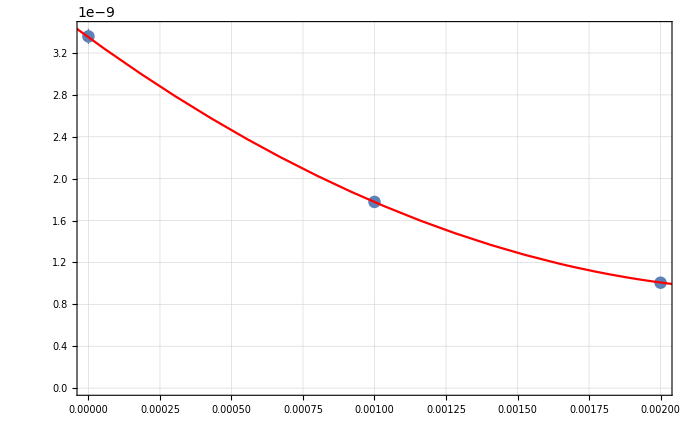
{b0 =  | 0.00245452
FittedModel[9.25267×10^-10+0.000402408 (-0.00245452+b)^2] | 
Missing[] | 
Missing[] | ,-Graphics-}

```mathematica
k2xfit=Chi2FitandPlot[BinInt35Binsk2xDataXOff[[All,2]]/Total[BinInt35Binsk2xDataXOff[[All,2]]],{BinInt35Binsk2xVary1XOff/Total[BinInt35Binsk2xVary1XOff[[All,2]]],BinInt35Binsk2xVary2XOff/Total[BinInt35Binsk2xVary2XOff[[All,2]]],BinInt35Binsk2xVary3XOff/Total[BinInt35Binsk2xVary3XOff[[All,2]]](*,BinInt35Binsk2xVary4/Total[BinInt35Binsk2xVary4[[All,2]]],BinInt35Binsk2xVary5/Total[BinInt35Binsk2xVary5[[All,2]]],BinInt35Binsk2xVary6/Total[BinInt35Binsk2xVary6[[All,2]]],BinInt35Binsk2xVary7/Total[BinInt35Binsk2xVary7[[All,2]]]*)},bList,5]
```

### old value was 1.95 with only 4 bvaries

```mathematica
k2xfit[[1,1,1,2]]/(10^-3)
```

4.3544

```mathematica
ListPlot3D[Transpose[{BinCentersBRamp[[2,All,1]],BinCentersBRamp[[2,All,2]],BinInt35BinsrFData[[All,2]]/Total[BinInt35BinsrFData[[All,2]]]}]]
```

-Graphics3D-